```mathematica
dmkpluspi00pfunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkpluspi2body0pfunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkplusleptefunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
dmkplusleptmufunct[m_,ep_]:=493/Sqrt[(m/2)^2-493^2]*(InterpolatingFunction[…][m/(2*493)*ep*(1+Sqrt[1-(2*493/m)^2])]-InterpolatingFunction[…][m/(2*493)*ep*(1-Sqrt[1-(2*493/m)^2])])
```

```mathematica
normfunc[dmm_,f_,ep_]:=NIntegrate[(f),{ep,0,dmm}]
```

```mathematica
dmkpluspi00pnorma[dmm_,ep_]:=(((4*0.017)/Quiet[normfunc[dmm,dmkpluspi00pfunct[dmm,ep],ep]])*dmkpluspi00pfunct[dmm,ep])
```

```mathematica
dmkpluspi2body0pnorma[dmm_,ep_]:=(((2*0.207)/Quiet[normfunc[dmm,dmkpluspi2body0pfunct[dmm,ep],ep]])*dmkpluspi2body0pfunct[dmm,ep])
```

```mathematica
dmkplusleptenorma[dmm_,ep_]:=(((2*0.05)/Quiet[normfunc[dmm,dmkplusleptefunct[dmm,ep],ep]])*dmkplusleptefunct[dmm,ep])
```

```mathematica
dmkplusleptmunorma[dmm_,ep_]:=(((2*0.034)/Quiet[normfunc[dmm,dmkplusleptmufunct[dmm,ep],ep]])*dmkplusleptmufunct[dmm,ep])
```

```mathematica
kplusminus[m_,emax_]:=Quiet[Plot[{Evaluate[dmkpluspi00pnorma[m,ep]],Evaluate[dmkpluspi2body0pnorma[m,ep]],Evaluate[dmkplusleptenorma[m,ep]],Evaluate[dmkplusleptmunorma[m,ep]],Evaluate[dmkpluspi00pnorma[m,ep]+dmkpluspi2body0pnorma[m,ep]+dmkplusleptenorma[m,ep]+dmkplusleptmunorma[m,ep]]},{ep,0,emax},PlotRange->Full,PlotStyle->  {Red,Blue,Green,Magenta,Black},PlotLegends->{"K+ -> π+π0π0","K+ -> π+π0","K+ -> e ν π0","K+ -> μ ν π0","1/2 Total K+ K-"},PlotLabel->m "MeV Dark Matter -> K+ K- Photon Spectrum" ]]
```

```mathematica
justtotalpm[m_]:=Quiet[Plot[Evaluate[dmkpluspi00pnorma[m,ep]+dmkpluspi2body0pnorma[m,ep]+dmkplusleptenorma[m,ep]+dmkplusleptmunorma[m,ep]],{ep,0,m},PlotRange->Full,PlotLegends-> {m "MeV"},PlotStyle->RandomColor[]]]
```

```mathematica
totalspreadpm[mlist_,x_]:=Show[(justtotalpm[#])&/@mlist,PlotRange-> {{0,x},Full}]
```

```mathematica
DM=1097.5
kfile[m_,ep_] :=
Evaluate[dmkpluspi00pnorma[DM,ep]+dmkpluspi2body0pnorma[DM,ep]+dmkplusleptenorma[DM,ep]+dmkplusleptmunorma[DM,ep]]
elist=N@Subdivide[0.01,1000,2000]
dataset={elist,kfile[DM, elist]}
SetDirectory@NotebookDirectory[]
Export["K+- PDFs\s"<>ToString[DM]<>".csv",dataset, "CSV"]
```

{{0.01,0.509995,1.00999,1.50999,2.00998,2.50998,3.00997,3.50997,4.00996,4.50996,5.00995,5.50995,6.00994,6.50994,7.00993,7.50993,8.00992,8.50992,9.00991,9.50991,10.0099,10.5099,11.0099,11.5099,12.0099,12.5099,13.0099,13.5099,14.0099,14.5099,15.0099,15.5098,16.0098,16.5098,17.0098,17.5098,18.0098,18.5098,19.0098,19.5098,20.0098,20.5098,21.0098,21.5098,22.0098,22.5098,23.0098,23.5098,24.0098,24.5098,25.0098,25.5097,26.0097,26.5097,27.0097,27.5097,28.0097,28.5097,29.0097,29.5097,30.0097,30.5097,31.0097,31.5097,32.0097,32.5097,33.0097,33.5097,34.0097,34.5097,35.0097,35.5096,36.0096,36.5096,37.0096,37.5096,38.0096,38.5096,39.0096,39.5096,40.0096,40.5096,41.0096,41.5096,42.0096,42.5096,43.0096,43.5096,44.0096,44.5096,45.0096,45.5095,46.0095,46.5095,47.0095,47.5095,48.0095,48.5095,49.0095,49.5095,50.0095,50.5095,51.0095,51.5095,52.0095,52.5095,53.0095,53.5095,54.0095,54.5095,55.0095,55.5094,56.0094,56.5094,57.0094,57.5094,58.0094,58.5094,59.0094,59.5094,60.0094,60.5094,61.0094,61.5094,62.0094,62.5094,63.0094,63.5094,64.0094,64.5094,65.0094,65.5093,66.0093,66.5093,67.0093,67.5093,68.0093,68.5093,69.0093,69.5093,70.0093,70.5093,71.0093,71.5093,72.0093,72.5093,73.0093,73.5093,74.0093,74.5093,75.0093,75.5092,76.0092,76.5092,77.0092,77.5092,78.0092,78.5092,79.0092,79.5092,80.0092,80.5092,81.0092,81.5092,82.0092,82.5092,83.0092,83.5092,84.0092,84.5092,85.0092,85.5091,86.0091,86.5091,87.0091,87.5091,88.0091,88.5091,89.0091,89.5091,90.0091,90.5091,91.0091,91.5091,92.0091,92.5091,93.0091,93.5091,94.0091,94.5091,95.0091,95.509,96.009,96.509,97.009,97.509,98.009,98.509,99.009,99.509,100.009,100.509,101.009,101.509,102.009,102.509,103.009,103.509,104.009,104.509,105.009,105.509,106.009,106.509,107.009,107.509,108.009,108.509,109.009,109.509,110.009,110.509,111.009,111.509,112.009,112.509,113.009,113.509,114.009,114.509,115.009,115.509,116.009,116.509,117.009,117.509,118.009,118.509,119.009,119.509,120.009,120.509,121.009,121.509,122.009,122.509,123.009,123.509,124.009,124.509,125.009,125.509,126.009,126.509,127.009,127.509,128.009,128.509,129.009,129.509,130.009,130.509,131.009,131.509,132.009,132.509,133.009,133.509,134.009,134.509,135.009,135.509,136.009,136.509,137.009,137.509,138.009,138.509,139.009,139.509,140.009,140.509,141.009,141.509,142.009,142.509,143.009,143.509,144.009,144.509,145.009,145.509,146.009,146.509,147.009,147.509,148.009,148.509,149.009,149.509,150.009,150.508,151.008,151.508,152.008,152.508,153.008,153.508,154.008,154.508,155.008,155.508,156.008,156.508,157.008,157.508,158.008,158.508,159.008,159.508,160.008,160.508,161.008,161.508,162.008,162.508,163.008,163.508,164.008,164.508,165.008,165.508,166.008,166.508,167.008,167.508,168.008,168.508,169.008,169.508,170.008,170.508,171.008,171.508,172.008,172.508,173.008,173.508,174.008,174.508,175.008,175.508,176.008,176.508,177.008,177.508,178.008,178.508,179.008,179.508,180.008,180.508,181.008,181.508,182.008,182.508,183.008,183.508,184.008,184.508,185.008,185.508,186.008,186.508,187.008,187.508,188.008,188.508,189.008,189.508,190.008,190.508,191.008,191.508,192.008,192.508,193.008,193.508,194.008,194.508,195.008,195.508,196.008,196.508,197.008,197.508,198.008,198.508,199.008,199.508,200.008,200.508,201.008,201.508,202.008,202.508,203.008,203.508,204.008,204.508,205.008,205.508,206.008,206.508,207.008,207.508,208.008,208.508,209.008,209.508,210.008,210.508,211.008,211.508,212.008,212.508,213.008,213.508,214.008,214.508,215.008,215.508,216.008,216.508,217.008,217.508,218.008,218.508,219.008,219.508,220.008,220.508,221.008,221.508,222.008,222.508,223.008,223.508,224.008,224.508,225.008,225.508,226.008,226.508,227.008,227.508,228.008,228.508,229.008,229.508,230.008,230.508,231.008,231.508,232.008,232.508,233.008,233.508,234.008,234.508,235.008,235.508,236.008,236.508,237.008,237.508,238.008,238.508,239.008,239.508,240.008,240.508,241.008,241.508,242.008,242.508,243.008,243.508,244.008,244.508,245.008,245.508,246.008,246.508,247.008,247.508,248.008,248.508,249.008,249.508,250.008,250.507,251.007,251.507,252.007,252.507,253.007,253.507,254.007,254.507,255.007,255.507,256.007,256.507,257.007,257.507,258.007,258.507,259.007,259.507,260.007,260.507,261.007,261.507,262.007,262.507,263.007,263.507,264.007,264.507,265.007,265.507,266.007,266.507,267.007,267.507,268.007,268.507,269.007,269.507,270.007,270.507,271.007,271.507,272.007,272.507,273.007,273.507,274.007,274.507,275.007,275.507,276.007,276.507,277.007,277.507,278.007,278.507,279.007,279.507,280.007,280.507,281.007,281.507,282.007,282.507,283.007,283.507,284.007,284.507,285.007,285.507,286.007,286.507,287.007,287.507,288.007,288.507,289.007,289.507,290.007,290.507,291.007,291.507,292.007,292.507,293.007,293.507,294.007,294.507,295.007,295.507,296.007,296.507,297.007,297.507,298.007,298.507,299.007,299.507,300.007,300.507,301.007,301.507,302.007,302.507,303.007,303.507,304.007,304.507,305.007,305.507,306.007,306.507,307.007,307.507,308.007,308.507,309.007,309.507,310.007,310.507,311.007,311.507,312.007,312.507,313.007,313.507,314.007,314.507,315.007,315.507,316.007,316.507,317.007,317.507,318.007,318.507,319.007,319.507,320.007,320.507,321.007,321.507,322.007,322.507,323.007,323.507,324.007,324.507,325.007,325.507,326.007,326.507,327.007,327.507,328.007,328.507,329.007,329.507,330.007,330.507,331.007,331.507,332.007,332.507,333.007,333.507,334.007,334.507,335.007,335.507,336.007,336.507,337.007,337.507,338.007,338.507,339.007,339.507,340.007,340.507,341.007,341.507,342.007,342.507,343.007,343.507,344.007,344.507,345.007,345.507,346.007,346.507,347.007,347.507,348.007,348.507,349.007,349.507,350.007,350.506,351.006,351.506,352.006,352.506,353.006,353.506,354.006,354.506,355.006,355.506,356.006,356.506,357.006,357.506,358.006,358.506,359.006,359.506,360.006,360.506,361.006,361.506,362.006,362.506,363.006,363.506,364.006,364.506,365.006,365.506,366.006,366.506,367.006,367.506,368.006,368.506,369.006,369.506,370.006,370.506,371.006,371.506,372.006,372.506,373.006,373.506,374.006,374.506,375.006,375.506,376.006,376.506,377.006,377.506,378.006,378.506,379.006,379.506,380.006,380.506,381.006,381.506,382.006,382.506,383.006,383.506,384.006,384.506,385.006,385.506,386.006,386.506,387.006,387.506,388.006,388.506,389.006,389.506,390.006,390.506,391.006,391.506,392.006,392.506,393.006,393.506,394.006,394.506,395.006,395.506,396.006,396.506,397.006,397.506,398.006,398.506,399.006,399.506,400.006,400.506,401.006,401.506,402.006,402.506,403.006,403.506,404.006,404.506,405.006,405.506,406.006,406.506,407.006,407.506,408.006,408.506,409.006,409.506,410.006,410.506,411.006,411.506,412.006,412.506,413.006,413.506,414.006,414.506,415.006,415.506,416.006,416.506,417.006,417.506,418.006,418.506,419.006,419.506,420.006,420.506,421.006,421.506,422.006,422.506,423.006,423.506,424.006,424.506,425.006,425.506,426.006,426.506,427.006,427.506,428.006,428.506,429.006,429.506,430.006,430.506,431.006,431.506,432.006,432.506,433.006,433.506,434.006,434.506,435.006,435.506,436.006,436.506,437.006,437.506,438.006,438.506,439.006,439.506,440.006,440.506,441.006,441.506,442.006,442.506,443.006,443.506,444.006,444.506,445.006,445.506,446.006,446.506,447.006,447.506,448.006,448.506,449.006,449.506,450.006,450.505,451.005,451.505,452.005,452.505,453.005,453.505,454.005,454.505,455.005,455.505,456.005,456.505,457.005,457.505,458.005,458.505,459.005,459.505,460.005,460.505,461.005,461.505,462.005,462.505,463.005,463.505,464.005,464.505,465.005,465.505,466.005,466.505,467.005,467.505,468.005,468.505,469.005,469.505,470.005,470.505,471.005,471.505,472.005,472.505,473.005,473.505,474.005,474.505,475.005,475.505,476.005,476.505,477.005,477.505,478.005,478.505,479.005,479.505,480.005,480.505,481.005,481.505,482.005,482.505,483.005,483.505,484.005,484.505,485.005,485.505,486.005,486.505,487.005,487.505,488.005,488.505,489.005,489.505,490.005,490.505,491.005,491.505,492.005,492.505,493.005,493.505,494.005,494.505,495.005,495.505,496.005,496.505,497.005,497.505,498.005,498.505,499.005,499.505,500.005,500.505,501.005,501.505,502.005,502.505,503.005,503.505,504.005,504.505,505.005,505.505,506.005,506.505,507.005,507.505,508.005,508.505,509.005,509.505,510.005,510.505,511.005,511.505,512.005,512.505,513.005,513.505,514.005,514.505,515.005,515.505,516.005,516.505,517.005,517.505,518.005,518.505,519.005,519.505,520.005,520.505,521.005,521.505,522.005,522.505,523.005,523.505,524.005,524.505,525.005,525.505,526.005,526.505,527.005,527.505,528.005,528.505,529.005,529.505,530.005,530.505,531.005,531.505,532.005,532.505,533.005,533.505,534.005,534.505,535.005,535.505,536.005,536.505,537.005,537.505,538.005,538.505,539.005,539.505,540.005,540.505,541.005,541.505,542.005,542.505,543.005,543.505,544.005,544.505,545.005,545.505,546.005,546.505,547.005,547.505,548.005,548.505,549.005,549.505,550.005,550.504,551.004,551.504,552.004,552.504,553.004,553.504,554.004,554.504,555.004,555.504,556.004,556.504,557.004,557.504,558.004,558.504,559.004,559.504,560.004,560.504,561.004,561.504,562.004,562.504,563.004,563.504,564.004,564.504,565.004,565.504,566.004,566.504,567.004,567.504,568.004,568.504,569.004,569.504,570.004,570.504,571.004,571.504,572.004,572.504,573.004,573.504,574.004,574.504,575.004,575.504,576.004,576.504,577.004,577.504,578.004,578.504,579.004,579.504,580.004,580.504,581.004,581.504,582.004,582.504,583.004,583.504,584.004,584.504,585.004,585.504,586.004,586.504,587.004,587.504,588.004,588.504,589.004,589.504,590.004,590.504,591.004,591.504,592.004,592.504,593.004,593.504,594.004,594.504,595.004,595.504,596.004,596.504,597.004,597.504,598.004,598.504,599.004,599.504,600.004,600.504,601.004,601.504,602.004,602.504,603.004,603.504,604.004,604.504,605.004,605.504,606.004,606.504,607.004,607.504,608.004,608.504,609.004,609.504,610.004,610.504,611.004,611.504,612.004,612.504,613.004,613.504,614.004,614.504,615.004,615.504,616.004,616.504,617.004,617.504,618.004,618.504,619.004,619.504,620.004,620.504,621.004,621.504,622.004,622.504,623.004,623.504,624.004,624.504,625.004,625.504,626.004,626.504,627.004,627.504,628.004,628.504,629.004,629.504,630.004,630.504,631.004,631.504,632.004,632.504,633.004,633.504,634.004,634.504,635.004,635.504,636.004,636.504,637.004,637.504,638.004,638.504,639.004,639.504,640.004,640.504,641.004,641.504,642.004,642.504,643.004,643.504,644.004,644.504,645.004,645.504,646.004,646.504,647.004,647.504,648.004,648.504,649.004,649.504,650.004,650.503,651.003,651.503,652.003,652.503,653.003,653.503,654.003,654.503,655.003,655.503,656.003,656.503,657.003,657.503,658.003,658.503,659.003,659.503,660.003,660.503,661.003,661.503,662.003,662.503,663.003,663.503,664.003,664.503,665.003,665.503,666.003,666.503,667.003,667.503,668.003,668.503,669.003,669.503,670.003,670.503,671.003,671.503,672.003,672.503,673.003,673.503,674.003,674.503,675.003,675.503,676.003,676.503,677.003,677.503,678.003,678.503,679.003,679.503,680.003,680.503,681.003,681.503,682.003,682.503,683.003,683.503,684.003,684.503,685.003,685.503,686.003,686.503,687.003,687.503,688.003,688.503,689.003,689.503,690.003,690.503,691.003,691.503,692.003,692.503,693.003,693.503,694.003,694.503,695.003,695.503,696.003,696.503,697.003,697.503,698.003,698.503,699.003,699.503,700.003,700.503,701.003,701.503,702.003,702.503,703.003,703.503,704.003,704.503,705.003,705.503,706.003,706.503,707.003,707.503,708.003,708.503,709.003,709.503,710.003,710.503,711.003,711.503,712.003,712.503,713.003,713.503,714.003,714.503,715.003,715.503,716.003,716.503,717.003,717.503,718.003,718.503,719.003,719.503,720.003,720.503,721.003,721.503,722.003,722.503,723.003,723.503,724.003,724.503,725.003,725.503,726.003,726.503,727.003,727.503,728.003,728.503,729.003,729.503,730.003,730.503,731.003,731.503,732.003,732.503,733.003,733.503,734.003,734.503,735.003,735.503,736.003,736.503,737.003,737.503,738.003,738.503,739.003,739.503,740.003,740.503,741.003,741.503,742.003,742.503,743.003,743.503,744.003,744.503,745.003,745.503,746.003,746.503,747.003,747.503,748.003,748.503,749.003,749.503,750.003,750.502,751.002,751.502,752.002,752.502,753.002,753.502,754.002,754.502,755.002,755.502,756.002,756.502,757.002,757.502,758.002,758.502,759.002,759.502,760.002,760.502,761.002,761.502,762.002,762.502,763.002,763.502,764.002,764.502,765.002,765.502,766.002,766.502,767.002,767.502,768.002,768.502,769.002,769.502,770.002,770.502,771.002,771.502,772.002,772.502,773.002,773.502,774.002,774.502,775.002,775.502,776.002,776.502,777.002,777.502,778.002,778.502,779.002,779.502,780.002,780.502,781.002,781.502,782.002,782.502,783.002,783.502,784.002,784.502,785.002,785.502,786.002,786.502,787.002,787.502,788.002,788.502,789.002,789.502,790.002,790.502,791.002,791.502,792.002,792.502,793.002,793.502,794.002,794.502,795.002,795.502,796.002,796.502,797.002,797.502,798.002,798.502,799.002,799.502,800.002,800.502,801.002,801.502,802.002,802.502,803.002,803.502,804.002,804.502,805.002,805.502,806.002,806.502,807.002,807.502,808.002,808.502,809.002,809.502,810.002,810.502,811.002,811.502,812.002,812.502,813.002,813.502,814.002,814.502,815.002,815.502,816.002,816.502,817.002,817.502,818.002,818.502,819.002,819.502,820.002,820.502,821.002,821.502,822.002,822.502,823.002,823.502,824.002,824.502,825.002,825.502,826.002,826.502,827.002,827.502,828.002,828.502,829.002,829.502,830.002,830.502,831.002,831.502,832.002,832.502,833.002,833.502,834.002,834.502,835.002,835.502,836.002,836.502,837.002,837.502,838.002,838.502,839.002,839.502,840.002,840.502,841.002,841.502,842.002,842.502,843.002,843.502,844.002,844.502,845.002,845.502,846.002,846.502,847.002,847.502,848.002,848.502,849.002,849.502,850.002,850.501,851.001,851.501,852.001,852.501,853.001,853.501,854.001,854.501,855.001,855.501,856.001,856.501,857.001,857.501,858.001,858.501,859.001,859.501,860.001,860.501,861.001,861.501,862.001,862.501,863.001,863.501,864.001,864.501,865.001,865.501,866.001,866.501,867.001,867.501,868.001,868.501,869.001,869.501,870.001,870.501,871.001,871.501,872.001,872.501,873.001,873.501,874.001,874.501,875.001,875.501,876.001,876.501,877.001,877.501,878.001,878.501,879.001,879.501,880.001,880.501,881.001,881.501,882.001,882.501,883.001,883.501,884.001,884.501,885.001,885.501,886.001,886.501,887.001,887.501,888.001,888.501,889.001,889.501,890.001,890.501,891.001,891.501,892.001,892.501,893.001,893.501,894.001,894.501,895.001,895.501,896.001,896.501,897.001,897.501,898.001,898.501,899.001,899.501,900.001,900.501,901.001,901.501,902.001,902.501,903.001,903.501,904.001,904.501,905.001,905.501,906.001,906.501,907.001,907.501,908.001,908.501,909.001,909.501,910.001,910.501,911.001,911.501,912.001,912.501,913.001,913.501,914.001,914.501,915.001,915.501,916.001,916.501,917.001,917.501,918.001,918.501,919.001,919.501,920.001,920.501,921.001,921.501,922.001,922.501,923.001,923.501,924.001,924.501,925.001,925.501,926.001,926.501,927.001,927.501,928.001,928.501,929.001,929.501,930.001,930.501,931.001,931.501,932.001,932.501,933.001,933.501,934.001,934.501,935.001,935.501,936.001,936.501,937.001,937.501,938.001,938.501,939.001,939.501,940.001,940.501,941.001,941.501,942.001,942.501,943.001,943.501,944.001,944.501,945.001,945.501,946.001,946.501,947.001,947.501,948.001,948.501,949.001,949.501,950.001,950.5,951.,951.5,952.,952.5,953.,953.5,954.,954.5,955.,955.5,956.,956.5,957.,957.5,958.,958.5,959.,959.5,960.,960.5,961.,961.5,962.,962.5,963.,963.5,964.,964.5,965.,965.5,966.,966.5,967.,967.5,968.,968.5,969.,969.5,970.,970.5,971.,971.5,972.,972.5,973.,973.5,974.,974.5,975.,975.5,976.,976.5,977.,977.5,978.,978.5,979.,979.5,980.,980.5,981.,981.5,982.,982.5,983.,983.5,984.,984.5,985.,985.5,986.,986.5,987.,987.5,988.,988.5,989.,989.5,990.,990.5,991.,991.5,992.,992.5,993.,993.5,994.,994.5,995.,995.5,996.,996.5,997.,997.5,998.,998.5,999.,999.5,1000.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-8.37073×10^-11,-6.30749×10^-11,-1.59837×10^-9,-3.03256×10^-6,0.0000128637,0.0000651494,0.000150785,0.000228822,0.000304254,0.000378229,0.000450744,0.000521925,0.000591821,0.000660537,0.000727886,0.000803613,0.000884861,0.000965976,0.00104754,0.00112951,0.00121176,0.00129418,0.00137667,0.00145909,0.00154136,0.00162337,0.00170504,0.00178629,0.00186705,0.00194726,0.00202688,0.00210585,0.00218414,0.00226171,0.00233854,0.00241461,0.00248991,0.0025644,0.00263915,0.00271384,0.00278551,0.00285204,0.00291147,0.00296476,0.00301096,0.0030475,0.00307976,0.00310999,0.00314363,0.00317712,0.00321032,0.00324286,0.00327491,0.00330647,0.00333756,0.00336816,0.00339828,0.00342792,0.00345708,0.00348577,0.00351401,0.00354181,0.00356906,0.00359586,0.00362234,0.00364874,0.00367449,0.00369854,0.00372003,0.00373913,0.00375676,0.00377371,0.00379021,0.00380618,0.00382152,0.00383624,0.00385035,0.00386386,0.0038768,0.00388917,0.00390099,0.00391227,0.00392303,0.00393329,0.00394305,0.00395233,0.00396114,0.0039695,0.00397743,0.00398492,0.003992,0.00399868,0.00400497,0.00401087,0.00401641,0.00402159,0.00402642,0.0040309,0.00403506,0.0040389,0.00404242,0.00404564,0.00404856,0.0040512,0.00405355,0.00405562,0.00405743,0.00405898,0.00406028,0.00406132,0.00406212,0.00406269,0.00406302,0.00406313,0.00406302,0.00406269,0.00406214,0.00406139,0.00406044,0.00405929,0.00405794,0.0040564,0.00405468,0.00405277,0.00405068,0.00404841,0.00404597,0.00404336,0.00404058,0.00403764,0.00403453,0.00403127,0.00402785,0.00402428,0.00402055,0.00401668,0.00401266,0.0040085,0.0040042,0.00399976,0.00399518,0.00399047,0.00398563,0.00398065,0.00397555,0.00397032,0.00396497,0.0039595,0.00395391,0.0039482,0.00394237,0.00393643,0.00393038,0.00392422,0.00391795,0.00391157,0.00390509,0.00389851,0.00389183,0.00388504,0.00387817,0.00387119,0.00386413,0.00385697,0.00384973,0.0038424,0.00383499,0.00382749,0.00381991,0.00381226,0.00380453,0.00379672,0.00378885,0.0037809,0.00377289,0.00376482,0.00375669,0.00374849,0.00374025,0.00373195,0.00372361,0.00371521,0.00370691,0.00369762,0.0036868,0.00367599,0.00366525,0.00365453,0.00364384,0.00363318,0.00362254,0.00361193,0.00360135,0.0035908,0.00358028,0.00356978,0.00355932,0.00354888,0.00353847,0.00352809,0.00351774,0.00350742,0.00349713,0.00348687,0.00347664,0.00346644,0.00345627,0.00344613,0.00343602,0.00342595,0.0034159,0.00340589,0.00339591,0.00338596,0.00337604,0.00336615,0.0033563,0.00334648,0.00333669,0.00332694,0.00331722,0.00330753,0.00329788,0.00328826,0.00327867,0.00326912,0.0032596,0.00325012,0.00324067,0.00323126,0.00322189,0.00321254,0.00320324,0.00319397,0.00318474,0.00317554,0.00316638,0.00315725,0.00314816,0.00313911,0.0031301,0.00312112,0.00311218,0.00310328,0.00309442,0.00308559,0.0030768,0.00306805,0.00305934,0.00305067,0.00304204,0.00303344,0.00302489,0.00301637,0.00300789,0.00299945,0.00299105,0.0029827,0.00297438,0.0029661,0.00295786,0.00294966,0.0029415,0.00293336,0.00292561,0.00291755,0.00290601,0.00289097,0.00287513,0.00285981,0.00284453,0.00282932,0.00281417,0.00279909,0.00278408,0.00276913,0.00275425,0.00273943,0.00272468,0.00270999,0.00269537,0.00268081,0.00266632,0.00265189,0.00263752,0.00262321,0.00260897,0.00259479,0.00258067,0.00256662,0.00255263,0.0025387,0.00252482,0.00251102,0.00249727,0.00248358,0.00246995,0.00245638,0.00244288,0.00242943,0.00241604,0.00240271,0.00238944,0.00237622,0.00236307,0.00234997,0.00233694,0.00232396,0.00231103,0.00229817,0.00228536,0.00227261,0.00225991,0.00224727,0.00223469,0.00222216,0.00220969,0.00219728,0.00218492,0.00217261,0.00216036,0.00214817,0.00213602,0.00212394,0.00211191,0.00209993,0.002088,0.00207613,0.00206431,0.00205255,0.00204083,0.00202917,0.00201757,0.00200601,0.00199451,0.00198306,0.00197166,0.00196031,0.00194901,0.00193777,0.00192657,0.00191543,0.00190434,0.00189329,0.0018823,0.00187136,0.00186047,0.00184962,0.00183883,0.00182808,0.00181739,0.00180674,0.00179615,0.0017856,0.0017751,0.00176464,0.00175424,0.00174388,0.00173357,0.00172331,0.0017131,0.00170293,0.00169281,0.00168274,0.00167271,0.00166273,0.0016528,0.00164291,0.00163307,0.00162327,0.00161352,0.00160382,0.00159416,0.00158455,0.00157498,0.00156545,0.00155597,0.00154653,0.00153714,0.0015278,0.00151849,0.00150923,0.00150002,0.00149084,0.00148171,0.00147263,0.00146358,0.00145458,0.00144562,0.00143671,0.00142784,0.001419,0.00141021,0.00140147,0.00139276,0.00138409,0.00137547,0.00136689,0.00135835,0.00134984,0.00134138,0.00133296,0.00132458,0.00131624,0.00130794,0.00129968,0.00129146,0.00128328,0.00127514,0.00126704,0.00125897,0.00125095,0.00124296,0.00123501,0.0012271,0.00121923,0.00121139,0.0012036,0.00119584,0.00118811,0.00118043,0.00117278,0.00116517,0.00115759,0.00115006,0.00114256,0.00113509,0.00112766,0.00112027,0.00111291,0.00110558,0.0010983,0.00109104,0.00108383,0.00107664,0.0010695,0.00106238,0.0010553,0.00104826,0.00104124,0.00103426,0.00102732,0.00102041,0.00101353,0.00100668,0.000999868,0.000993087,0.000986338,0.000979621,0.000972936,0.000966283,0.000959661,0.000953071,0.000946511,0.000939983,0.000933485,0.000927017,0.00092058,0.000914172,0.000907795,0.000901447,0.000895128,0.000888839,0.000882578,0.000876346,0.000870142,0.000863967,0.00085782,0.0008517,0.000845607,0.000839542,0.000833503,0.000827491,0.000821506,0.000815543,0.000809602,0.0008037,0.000797823,0.000791953,0.000786044,0.000780194,0.000774571,0.000769327,0.000764424,0.00075969,0.000754978,0.000750242,0.000745499,0.00074077,0.000736053,0.00073135,0.000726659,0.000721982,0.000717318,0.000712666,0.000708027,0.000703401,0.000698788,0.000694187,0.000689599,0.000685023,0.00068046,0.00067591,0.000671371,0.000666845,0.000662331,0.00065783,0.00065334,0.000648863,0.000644398,0.000639944,0.000635503,0.000631073,0.000626655,0.000622249,0.000617855,0.000613472,0.000609101,0.000604742,0.000600394,0.000596057,0.000591732,0.000587418,0.000583115,0.000578824,0.000574544,0.000570275,0.000566016,0.000561769,0.000557533,0.000553308,0.000549094,0.00054489,0.000540698,0.000536516,0.000532344,0.000528183,0.000524033,0.000519893,0.000515764,0.000511645,0.000507536,0.000503438,0.00049935,0.000495272,0.000491205,0.000487147,0.000483099,0.000479062,0.000475034,0.000471017,0.000467009,0.000463011,0.000459022,0.000455044,0.000451075,0.000447115,0.000443165,0.000439225,0.000435294,0.000431373,0.000427461,0.000423558,0.000419664,0.00041578,0.000411905,0.000408039,0.000404182,0.000400334,0.000396495,0.000392665,0.000388844,0.000385032,0.000381228,0.000377433,0.000373647,0.00036987,0.000366101,0.000362341,0.00035859,0.000354846,0.000351112,0.000347385,0.000343667,0.000339957,0.000336256,0.000332563,0.000328878,0.000325201,0.000321532,0.000317871,0.000314218,0.000310573,0.000306936,0.000303307,0.000299685,0.000296072,0.000292466,0.000288868,0.000285277,0.000281694,0.000278119,0.000274551,0.00027099,0.000267437,0.000263892,0.000260353,0.000256822,0.000253299,0.000249782,0.000246273,0.000242771,0.000239276,0.000235788,0.000232307,0.000228833,0.000225366,0.000221906,0.000218452,0.000215006,0.000211566,0.000208133,0.000204707,0.000201288,0.000197875,0.000194468,0.000191068,0.000187675,0.000184288,0.000180908,0.000177534,0.000174166,0.000170805,0.00016745,0.000164101,0.000160759,0.000157423,0.000154092,0.000150768,0.00014745,0.000144138,0.000140832,0.000137532,0.000134238,0.00013095,0.000127667,0.000124391,0.00012112,0.000117855,0.000114596,0.000111342,0.000108094,0.000104852,0.000101615,0.0000983839,0.0000951582,0.000091938,0.0000887232,0.0000855139,0.0000823099,0.0000791113,0.000075918,0.00007273,0.0000695473,0.0000663698,0.0000631975,0.0000600303,0.0000568683,0.0000537114,0.0000505596,0.0000474128,0.000044271,0.0000411342,0.0000380023,0.0000348754,0.0000317534,0.0000286362,0.0000255239,0.0000224285,0.0000193388,0.0000162333,0.0000129574,9.55863×10^-6,6.38765×10^-6,3.71964×10^-6,1.77943×10^-6,3.71756×10^-7,-4.50667×10^-7,-5.47137×10^-7,-3.2752×10^-7,1.19057×10^-8,3.33559×10^-8,2.7717×10^-8,8.0022×10^-9,4.97637×10^-9,4.07064×10^-9,3.29031×10^-9,2.6242×10^-9,2.06156×10^-9,1.59202×10^-9,1.20545×10^-9,8.92166×10^-10,6.43021×10^-10,4.49148×10^-10,3.02117×10^-10,1.94198×10^-10,1.18142×10^-10,6.7209×10^-11,3.57373×10^-11,1.81135×10^-11,9.2007×10^-12,4.45653×10^-12,1.58044×10^-12,2.123×10^-13,-2.20959×10^-13,-3.06868×10^-13,-2.04741×10^-13,-5.95782×10^-14,-1.14013×10^-15,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

C:\Users\jacob\Desktop\EtaPion

K+- PDFs\s1087.5.csv

1097.5

{0.01,0.509995,1.00999,1.50999,2.00998,2.50998,3.00997,3.50997,4.00996,4.50996,5.00995,5.50995,6.00994,6.50994,7.00993,7.50993,8.00992,8.50992,9.00991,9.50991,10.0099,10.5099,11.0099,11.5099,12.0099,12.5099,13.0099,13.5099,14.0099,14.5099,15.0099,15.5098,16.0098,16.5098,17.0098,17.5098,18.0098,18.5098,19.0098,19.5098,20.0098,20.5098,21.0098,21.5098,22.0098,22.5098,23.0098,23.5098,24.0098,24.5098,25.0098,25.5097,26.0097,26.5097,27.0097,27.5097,28.0097,28.5097,29.0097,29.5097,30.0097,30.5097,31.0097,31.5097,32.0097,32.5097,33.0097,33.5097,34.0097,34.5097,35.0097,35.5096,36.0096,36.5096,37.0096,37.5096,38.0096,38.5096,39.0096,39.5096,40.0096,40.5096,41.0096,41.5096,42.0096,42.5096,43.0096,43.5096,44.0096,44.5096,45.0096,45.5095,46.0095,46.5095,47.0095,47.5095,48.0095,48.5095,49.0095,49.5095,50.0095,50.5095,51.0095,51.5095,52.0095,52.5095,53.0095,53.5095,54.0095,54.5095,55.0095,55.5094,56.0094,56.5094,57.0094,57.5094,58.0094,58.5094,59.0094,59.5094,60.0094,60.5094,61.0094,61.5094,62.0094,62.5094,63.0094,63.5094,64.0094,64.5094,65.0094,65.5093,66.0093,66.5093,67.0093,67.5093,68.0093,68.5093,69.0093,69.5093,70.0093,70.5093,71.0093,71.5093,72.0093,72.5093,73.0093,73.5093,74.0093,74.5093,75.0093,75.5092,76.0092,76.5092,77.0092,77.5092,78.0092,78.5092,79.0092,79.5092,80.0092,80.5092,81.0092,81.5092,82.0092,82.5092,83.0092,83.5092,84.0092,84.5092,85.0092,85.5091,86.0091,86.5091,87.0091,87.5091,88.0091,88.5091,89.0091,89.5091,90.0091,90.5091,91.0091,91.5091,92.0091,92.5091,93.0091,93.5091,94.0091,94.5091,95.0091,95.509,96.009,96.509,97.009,97.509,98.009,98.509,99.009,99.509,100.009,100.509,101.009,101.509,102.009,102.509,103.009,103.509,104.009,104.509,105.009,105.509,106.009,106.509,107.009,107.509,108.009,108.509,109.009,109.509,110.009,110.509,111.009,111.509,112.009,112.509,113.009,113.509,114.009,114.509,115.009,115.509,116.009,116.509,117.009,117.509,118.009,118.509,119.009,119.509,120.009,120.509,121.009,121.509,122.009,122.509,123.009,123.509,124.009,124.509,125.009,125.509,126.009,126.509,127.009,127.509,128.009,128.509,129.009,129.509,130.009,130.509,131.009,131.509,132.009,132.509,133.009,133.509,134.009,134.509,135.009,135.509,136.009,136.509,137.009,137.509,138.009,138.509,139.009,139.509,140.009,140.509,141.009,141.509,142.009,142.509,143.009,143.509,144.009,144.509,145.009,145.509,146.009,146.509,147.009,147.509,148.009,148.509,149.009,149.509,150.009,150.508,151.008,151.508,152.008,152.508,153.008,153.508,154.008,154.508,155.008,155.508,156.008,156.508,157.008,157.508,158.008,158.508,159.008,159.508,160.008,160.508,161.008,161.508,162.008,162.508,163.008,163.508,164.008,164.508,165.008,165.508,166.008,166.508,167.008,167.508,168.008,168.508,169.008,169.508,170.008,170.508,171.008,171.508,172.008,172.508,173.008,173.508,174.008,174.508,175.008,175.508,176.008,176.508,177.008,177.508,178.008,178.508,179.008,179.508,180.008,180.508,181.008,181.508,182.008,182.508,183.008,183.508,184.008,184.508,185.008,185.508,186.008,186.508,187.008,187.508,188.008,188.508,189.008,189.508,190.008,190.508,191.008,191.508,192.008,192.508,193.008,193.508,194.008,194.508,195.008,195.508,196.008,196.508,197.008,197.508,198.008,198.508,199.008,199.508,200.008,200.508,201.008,201.508,202.008,202.508,203.008,203.508,204.008,204.508,205.008,205.508,206.008,206.508,207.008,207.508,208.008,208.508,209.008,209.508,210.008,210.508,211.008,211.508,212.008,212.508,213.008,213.508,214.008,214.508,215.008,215.508,216.008,216.508,217.008,217.508,218.008,218.508,219.008,219.508,220.008,220.508,221.008,221.508,222.008,222.508,223.008,223.508,224.008,224.508,225.008,225.508,226.008,226.508,227.008,227.508,228.008,228.508,229.008,229.508,230.008,230.508,231.008,231.508,232.008,232.508,233.008,233.508,234.008,234.508,235.008,235.508,236.008,236.508,237.008,237.508,238.008,238.508,239.008,239.508,240.008,240.508,241.008,241.508,242.008,242.508,243.008,243.508,244.008,244.508,245.008,245.508,246.008,246.508,247.008,247.508,248.008,248.508,249.008,249.508,250.008,250.507,251.007,251.507,252.007,252.507,253.007,253.507,254.007,254.507,255.007,255.507,256.007,256.507,257.007,257.507,258.007,258.507,259.007,259.507,260.007,260.507,261.007,261.507,262.007,262.507,263.007,263.507,264.007,264.507,265.007,265.507,266.007,266.507,267.007,267.507,268.007,268.507,269.007,269.507,270.007,270.507,271.007,271.507,272.007,272.507,273.007,273.507,274.007,274.507,275.007,275.507,276.007,276.507,277.007,277.507,278.007,278.507,279.007,279.507,280.007,280.507,281.007,281.507,282.007,282.507,283.007,283.507,284.007,284.507,285.007,285.507,286.007,286.507,287.007,287.507,288.007,288.507,289.007,289.507,290.007,290.507,291.007,291.507,292.007,292.507,293.007,293.507,294.007,294.507,295.007,295.507,296.007,296.507,297.007,297.507,298.007,298.507,299.007,299.507,300.007,300.507,301.007,301.507,302.007,302.507,303.007,303.507,304.007,304.507,305.007,305.507,306.007,306.507,307.007,307.507,308.007,308.507,309.007,309.507,310.007,310.507,311.007,311.507,312.007,312.507,313.007,313.507,314.007,314.507,315.007,315.507,316.007,316.507,317.007,317.507,318.007,318.507,319.007,319.507,320.007,320.507,321.007,321.507,322.007,322.507,323.007,323.507,324.007,324.507,325.007,325.507,326.007,326.507,327.007,327.507,328.007,328.507,329.007,329.507,330.007,330.507,331.007,331.507,332.007,332.507,333.007,333.507,334.007,334.507,335.007,335.507,336.007,336.507,337.007,337.507,338.007,338.507,339.007,339.507,340.007,340.507,341.007,341.507,342.007,342.507,343.007,343.507,344.007,344.507,345.007,345.507,346.007,346.507,347.007,347.507,348.007,348.507,349.007,349.507,350.007,350.506,351.006,351.506,352.006,352.506,353.006,353.506,354.006,354.506,355.006,355.506,356.006,356.506,357.006,357.506,358.006,358.506,359.006,359.506,360.006,360.506,361.006,361.506,362.006,362.506,363.006,363.506,364.006,364.506,365.006,365.506,366.006,366.506,367.006,367.506,368.006,368.506,369.006,369.506,370.006,370.506,371.006,371.506,372.006,372.506,373.006,373.506,374.006,374.506,375.006,375.506,376.006,376.506,377.006,377.506,378.006,378.506,379.006,379.506,380.006,380.506,381.006,381.506,382.006,382.506,383.006,383.506,384.006,384.506,385.006,385.506,386.006,386.506,387.006,387.506,388.006,388.506,389.006,389.506,390.006,390.506,391.006,391.506,392.006,392.506,393.006,393.506,394.006,394.506,395.006,395.506,396.006,396.506,397.006,397.506,398.006,398.506,399.006,399.506,400.006,400.506,401.006,401.506,402.006,402.506,403.006,403.506,404.006,404.506,405.006,405.506,406.006,406.506,407.006,407.506,408.006,408.506,409.006,409.506,410.006,410.506,411.006,411.506,412.006,412.506,413.006,413.506,414.006,414.506,415.006,415.506,416.006,416.506,417.006,417.506,418.006,418.506,419.006,419.506,420.006,420.506,421.006,421.506,422.006,422.506,423.006,423.506,424.006,424.506,425.006,425.506,426.006,426.506,427.006,427.506,428.006,428.506,429.006,429.506,430.006,430.506,431.006,431.506,432.006,432.506,433.006,433.506,434.006,434.506,435.006,435.506,436.006,436.506,437.006,437.506,438.006,438.506,439.006,439.506,440.006,440.506,441.006,441.506,442.006,442.506,443.006,443.506,444.006,444.506,445.006,445.506,446.006,446.506,447.006,447.506,448.006,448.506,449.006,449.506,450.006,450.505,451.005,451.505,452.005,452.505,453.005,453.505,454.005,454.505,455.005,455.505,456.005,456.505,457.005,457.505,458.005,458.505,459.005,459.505,460.005,460.505,461.005,461.505,462.005,462.505,463.005,463.505,464.005,464.505,465.005,465.505,466.005,466.505,467.005,467.505,468.005,468.505,469.005,469.505,470.005,470.505,471.005,471.505,472.005,472.505,473.005,473.505,474.005,474.505,475.005,475.505,476.005,476.505,477.005,477.505,478.005,478.505,479.005,479.505,480.005,480.505,481.005,481.505,482.005,482.505,483.005,483.505,484.005,484.505,485.005,485.505,486.005,486.505,487.005,487.505,488.005,488.505,489.005,489.505,490.005,490.505,491.005,491.505,492.005,492.505,493.005,493.505,494.005,494.505,495.005,495.505,496.005,496.505,497.005,497.505,498.005,498.505,499.005,499.505,500.005,500.505,501.005,501.505,502.005,502.505,503.005,503.505,504.005,504.505,505.005,505.505,506.005,506.505,507.005,507.505,508.005,508.505,509.005,509.505,510.005,510.505,511.005,511.505,512.005,512.505,513.005,513.505,514.005,514.505,515.005,515.505,516.005,516.505,517.005,517.505,518.005,518.505,519.005,519.505,520.005,520.505,521.005,521.505,522.005,522.505,523.005,523.505,524.005,524.505,525.005,525.505,526.005,526.505,527.005,527.505,528.005,528.505,529.005,529.505,530.005,530.505,531.005,531.505,532.005,532.505,533.005,533.505,534.005,534.505,535.005,535.505,536.005,536.505,537.005,537.505,538.005,538.505,539.005,539.505,540.005,540.505,541.005,541.505,542.005,542.505,543.005,543.505,544.005,544.505,545.005,545.505,546.005,546.505,547.005,547.505,548.005,548.505,549.005,549.505,550.005,550.504,551.004,551.504,552.004,552.504,553.004,553.504,554.004,554.504,555.004,555.504,556.004,556.504,557.004,557.504,558.004,558.504,559.004,559.504,560.004,560.504,561.004,561.504,562.004,562.504,563.004,563.504,564.004,564.504,565.004,565.504,566.004,566.504,567.004,567.504,568.004,568.504,569.004,569.504,570.004,570.504,571.004,571.504,572.004,572.504,573.004,573.504,574.004,574.504,575.004,575.504,576.004,576.504,577.004,577.504,578.004,578.504,579.004,579.504,580.004,580.504,581.004,581.504,582.004,582.504,583.004,583.504,584.004,584.504,585.004,585.504,586.004,586.504,587.004,587.504,588.004,588.504,589.004,589.504,590.004,590.504,591.004,591.504,592.004,592.504,593.004,593.504,594.004,594.504,595.004,595.504,596.004,596.504,597.004,597.504,598.004,598.504,599.004,599.504,600.004,600.504,601.004,601.504,602.004,602.504,603.004,603.504,604.004,604.504,605.004,605.504,606.004,606.504,607.004,607.504,608.004,608.504,609.004,609.504,610.004,610.504,611.004,611.504,612.004,612.504,613.004,613.504,614.004,614.504,615.004,615.504,616.004,616.504,617.004,617.504,618.004,618.504,619.004,619.504,620.004,620.504,621.004,621.504,622.004,622.504,623.004,623.504,624.004,624.504,625.004,625.504,626.004,626.504,627.004,627.504,628.004,628.504,629.004,629.504,630.004,630.504,631.004,631.504,632.004,632.504,633.004,633.504,634.004,634.504,635.004,635.504,636.004,636.504,637.004,637.504,638.004,638.504,639.004,639.504,640.004,640.504,641.004,641.504,642.004,642.504,643.004,643.504,644.004,644.504,645.004,645.504,646.004,646.504,647.004,647.504,648.004,648.504,649.004,649.504,650.004,650.503,651.003,651.503,652.003,652.503,653.003,653.503,654.003,654.503,655.003,655.503,656.003,656.503,657.003,657.503,658.003,658.503,659.003,659.503,660.003,660.503,661.003,661.503,662.003,662.503,663.003,663.503,664.003,664.503,665.003,665.503,666.003,666.503,667.003,667.503,668.003,668.503,669.003,669.503,670.003,670.503,671.003,671.503,672.003,672.503,673.003,673.503,674.003,674.503,675.003,675.503,676.003,676.503,677.003,677.503,678.003,678.503,679.003,679.503,680.003,680.503,681.003,681.503,682.003,682.503,683.003,683.503,684.003,684.503,685.003,685.503,686.003,686.503,687.003,687.503,688.003,688.503,689.003,689.503,690.003,690.503,691.003,691.503,692.003,692.503,693.003,693.503,694.003,694.503,695.003,695.503,696.003,696.503,697.003,697.503,698.003,698.503,699.003,699.503,700.003,700.503,701.003,701.503,702.003,702.503,703.003,703.503,704.003,704.503,705.003,705.503,706.003,706.503,707.003,707.503,708.003,708.503,709.003,709.503,710.003,710.503,711.003,711.503,712.003,712.503,713.003,713.503,714.003,714.503,715.003,715.503,716.003,716.503,717.003,717.503,718.003,718.503,719.003,719.503,720.003,720.503,721.003,721.503,722.003,722.503,723.003,723.503,724.003,724.503,725.003,725.503,726.003,726.503,727.003,727.503,728.003,728.503,729.003,729.503,730.003,730.503,731.003,731.503,732.003,732.503,733.003,733.503,734.003,734.503,735.003,735.503,736.003,736.503,737.003,737.503,738.003,738.503,739.003,739.503,740.003,740.503,741.003,741.503,742.003,742.503,743.003,743.503,744.003,744.503,745.003,745.503,746.003,746.503,747.003,747.503,748.003,748.503,749.003,749.503,750.003,750.502,751.002,751.502,752.002,752.502,753.002,753.502,754.002,754.502,755.002,755.502,756.002,756.502,757.002,757.502,758.002,758.502,759.002,759.502,760.002,760.502,761.002,761.502,762.002,762.502,763.002,763.502,764.002,764.502,765.002,765.502,766.002,766.502,767.002,767.502,768.002,768.502,769.002,769.502,770.002,770.502,771.002,771.502,772.002,772.502,773.002,773.502,774.002,774.502,775.002,775.502,776.002,776.502,777.002,777.502,778.002,778.502,779.002,779.502,780.002,780.502,781.002,781.502,782.002,782.502,783.002,783.502,784.002,784.502,785.002,785.502,786.002,786.502,787.002,787.502,788.002,788.502,789.002,789.502,790.002,790.502,791.002,791.502,792.002,792.502,793.002,793.502,794.002,794.502,795.002,795.502,796.002,796.502,797.002,797.502,798.002,798.502,799.002,799.502,800.002,800.502,801.002,801.502,802.002,802.502,803.002,803.502,804.002,804.502,805.002,805.502,806.002,806.502,807.002,807.502,808.002,808.502,809.002,809.502,810.002,810.502,811.002,811.502,812.002,812.502,813.002,813.502,814.002,814.502,815.002,815.502,816.002,816.502,817.002,817.502,818.002,818.502,819.002,819.502,820.002,820.502,821.002,821.502,822.002,822.502,823.002,823.502,824.002,824.502,825.002,825.502,826.002,826.502,827.002,827.502,828.002,828.502,829.002,829.502,830.002,830.502,831.002,831.502,832.002,832.502,833.002,833.502,834.002,834.502,835.002,835.502,836.002,836.502,837.002,837.502,838.002,838.502,839.002,839.502,840.002,840.502,841.002,841.502,842.002,842.502,843.002,843.502,844.002,844.502,845.002,845.502,846.002,846.502,847.002,847.502,848.002,848.502,849.002,849.502,850.002,850.501,851.001,851.501,852.001,852.501,853.001,853.501,854.001,854.501,855.001,855.501,856.001,856.501,857.001,857.501,858.001,858.501,859.001,859.501,860.001,860.501,861.001,861.501,862.001,862.501,863.001,863.501,864.001,864.501,865.001,865.501,866.001,866.501,867.001,867.501,868.001,868.501,869.001,869.501,870.001,870.501,871.001,871.501,872.001,872.501,873.001,873.501,874.001,874.501,875.001,875.501,876.001,876.501,877.001,877.501,878.001,878.501,879.001,879.501,880.001,880.501,881.001,881.501,882.001,882.501,883.001,883.501,884.001,884.501,885.001,885.501,886.001,886.501,887.001,887.501,888.001,888.501,889.001,889.501,890.001,890.501,891.001,891.501,892.001,892.501,893.001,893.501,894.001,894.501,895.001,895.501,896.001,896.501,897.001,897.501,898.001,898.501,899.001,899.501,900.001,900.501,901.001,901.501,902.001,902.501,903.001,903.501,904.001,904.501,905.001,905.501,906.001,906.501,907.001,907.501,908.001,908.501,909.001,909.501,910.001,910.501,911.001,911.501,912.001,912.501,913.001,913.501,914.001,914.501,915.001,915.501,916.001,916.501,917.001,917.501,918.001,918.501,919.001,919.501,920.001,920.501,921.001,921.501,922.001,922.501,923.001,923.501,924.001,924.501,925.001,925.501,926.001,926.501,927.001,927.501,928.001,928.501,929.001,929.501,930.001,930.501,931.001,931.501,932.001,932.501,933.001,933.501,934.001,934.501,935.001,935.501,936.001,936.501,937.001,937.501,938.001,938.501,939.001,939.501,940.001,940.501,941.001,941.501,942.001,942.501,943.001,943.501,944.001,944.501,945.001,945.501,946.001,946.501,947.001,947.501,948.001,948.501,949.001,949.501,950.001,950.5,951.,951.5,952.,952.5,953.,953.5,954.,954.5,955.,955.5,956.,956.5,957.,957.5,958.,958.5,959.,959.5,960.,960.5,961.,961.5,962.,962.5,963.,963.5,964.,964.5,965.,965.5,966.,966.5,967.,967.5,968.,968.5,969.,969.5,970.,970.5,971.,971.5,972.,972.5,973.,973.5,974.,974.5,975.,975.5,976.,976.5,977.,977.5,978.,978.5,979.,979.5,980.,980.5,981.,981.5,982.,982.5,983.,983.5,984.,984.5,985.,985.5,986.,986.5,987.,987.5,988.,988.5,989.,989.5,990.,990.5,991.,991.5,992.,992.5,993.,993.5,994.,994.5,995.,995.5,996.,996.5,997.,997.5,998.,998.5,999.,999.5,1000.}

InterpolatingFunction::dmval: Input value {1000.4} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1001.2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1002.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,0.509995,1.00999,1.50999,2.00998,2.50998,3.00997,3.50997,4.00996,4.50996,5.00995,5.50995,6.00994,6.50994,7.00993,7.50993,8.00992,8.50992,9.00991,9.50991,10.0099,10.5099,11.0099,11.5099,12.0099,12.5099,13.0099,13.5099,14.0099,14.5099,15.0099,15.5098,16.0098,16.5098,17.0098,17.5098,18.0098,18.5098,19.0098,19.5098,20.0098,20.5098,21.0098,21.5098,22.0098,22.5098,23.0098,23.5098,24.0098,24.5098,25.0098,25.5097,26.0097,26.5097,27.0097,27.5097,28.0097,28.5097,29.0097,29.5097,30.0097,30.5097,31.0097,31.5097,32.0097,32.5097,33.0097,33.5097,34.0097,34.5097,35.0097,35.5096,36.0096,36.5096,37.0096,37.5096,38.0096,38.5096,39.0096,39.5096,40.0096,40.5096,41.0096,41.5096,42.0096,42.5096,43.0096,43.5096,44.0096,44.5096,45.0096,45.5095,46.0095,46.5095,47.0095,47.5095,48.0095,48.5095,49.0095,49.5095,50.0095,50.5095,51.0095,51.5095,52.0095,52.5095,53.0095,53.5095,54.0095,54.5095,55.0095,55.5094,56.0094,56.5094,57.0094,57.5094,58.0094,58.5094,59.0094,59.5094,60.0094,60.5094,61.0094,61.5094,62.0094,62.5094,63.0094,63.5094,64.0094,64.5094,65.0094,65.5093,66.0093,66.5093,67.0093,67.5093,68.0093,68.5093,69.0093,69.5093,70.0093,70.5093,71.0093,71.5093,72.0093,72.5093,73.0093,73.5093,74.0093,74.5093,75.0093,75.5092,76.0092,76.5092,77.0092,77.5092,78.0092,78.5092,79.0092,79.5092,80.0092,80.5092,81.0092,81.5092,82.0092,82.5092,83.0092,83.5092,84.0092,84.5092,85.0092,85.5091,86.0091,86.5091,87.0091,87.5091,88.0091,88.5091,89.0091,89.5091,90.0091,90.5091,91.0091,91.5091,92.0091,92.5091,93.0091,93.5091,94.0091,94.5091,95.0091,95.509,96.009,96.509,97.009,97.509,98.009,98.509,99.009,99.509,100.009,100.509,101.009,101.509,102.009,102.509,103.009,103.509,104.009,104.509,105.009,105.509,106.009,106.509,107.009,107.509,108.009,108.509,109.009,109.509,110.009,110.509,111.009,111.509,112.009,112.509,113.009,113.509,114.009,114.509,115.009,115.509,116.009,116.509,117.009,117.509,118.009,118.509,119.009,119.509,120.009,120.509,121.009,121.509,122.009,122.509,123.009,123.509,124.009,124.509,125.009,125.509,126.009,126.509,127.009,127.509,128.009,128.509,129.009,129.509,130.009,130.509,131.009,131.509,132.009,132.509,133.009,133.509,134.009,134.509,135.009,135.509,136.009,136.509,137.009,137.509,138.009,138.509,139.009,139.509,140.009,140.509,141.009,141.509,142.009,142.509,143.009,143.509,144.009,144.509,145.009,145.509,146.009,146.509,147.009,147.509,148.009,148.509,149.009,149.509,150.009,150.508,151.008,151.508,152.008,152.508,153.008,153.508,154.008,154.508,155.008,155.508,156.008,156.508,157.008,157.508,158.008,158.508,159.008,159.508,160.008,160.508,161.008,161.508,162.008,162.508,163.008,163.508,164.008,164.508,165.008,165.508,166.008,166.508,167.008,167.508,168.008,168.508,169.008,169.508,170.008,170.508,171.008,171.508,172.008,172.508,173.008,173.508,174.008,174.508,175.008,175.508,176.008,176.508,177.008,177.508,178.008,178.508,179.008,179.508,180.008,180.508,181.008,181.508,182.008,182.508,183.008,183.508,184.008,184.508,185.008,185.508,186.008,186.508,187.008,187.508,188.008,188.508,189.008,189.508,190.008,190.508,191.008,191.508,192.008,192.508,193.008,193.508,194.008,194.508,195.008,195.508,196.008,196.508,197.008,197.508,198.008,198.508,199.008,199.508,200.008,200.508,201.008,201.508,202.008,202.508,203.008,203.508,204.008,204.508,205.008,205.508,206.008,206.508,207.008,207.508,208.008,208.508,209.008,209.508,210.008,210.508,211.008,211.508,212.008,212.508,213.008,213.508,214.008,214.508,215.008,215.508,216.008,216.508,217.008,217.508,218.008,218.508,219.008,219.508,220.008,220.508,221.008,221.508,222.008,222.508,223.008,223.508,224.008,224.508,225.008,225.508,226.008,226.508,227.008,227.508,228.008,228.508,229.008,229.508,230.008,230.508,231.008,231.508,232.008,232.508,233.008,233.508,234.008,234.508,235.008,235.508,236.008,236.508,237.008,237.508,238.008,238.508,239.008,239.508,240.008,240.508,241.008,241.508,242.008,242.508,243.008,243.508,244.008,244.508,245.008,245.508,246.008,246.508,247.008,247.508,248.008,248.508,249.008,249.508,250.008,250.507,251.007,251.507,252.007,252.507,253.007,253.507,254.007,254.507,255.007,255.507,256.007,256.507,257.007,257.507,258.007,258.507,259.007,259.507,260.007,260.507,261.007,261.507,262.007,262.507,263.007,263.507,264.007,264.507,265.007,265.507,266.007,266.507,267.007,267.507,268.007,268.507,269.007,269.507,270.007,270.507,271.007,271.507,272.007,272.507,273.007,273.507,274.007,274.507,275.007,275.507,276.007,276.507,277.007,277.507,278.007,278.507,279.007,279.507,280.007,280.507,281.007,281.507,282.007,282.507,283.007,283.507,284.007,284.507,285.007,285.507,286.007,286.507,287.007,287.507,288.007,288.507,289.007,289.507,290.007,290.507,291.007,291.507,292.007,292.507,293.007,293.507,294.007,294.507,295.007,295.507,296.007,296.507,297.007,297.507,298.007,298.507,299.007,299.507,300.007,300.507,301.007,301.507,302.007,302.507,303.007,303.507,304.007,304.507,305.007,305.507,306.007,306.507,307.007,307.507,308.007,308.507,309.007,309.507,310.007,310.507,311.007,311.507,312.007,312.507,313.007,313.507,314.007,314.507,315.007,315.507,316.007,316.507,317.007,317.507,318.007,318.507,319.007,319.507,320.007,320.507,321.007,321.507,322.007,322.507,323.007,323.507,324.007,324.507,325.007,325.507,326.007,326.507,327.007,327.507,328.007,328.507,329.007,329.507,330.007,330.507,331.007,331.507,332.007,332.507,333.007,333.507,334.007,334.507,335.007,335.507,336.007,336.507,337.007,337.507,338.007,338.507,339.007,339.507,340.007,340.507,341.007,341.507,342.007,342.507,343.007,343.507,344.007,344.507,345.007,345.507,346.007,346.507,347.007,347.507,348.007,348.507,349.007,349.507,350.007,350.506,351.006,351.506,352.006,352.506,353.006,353.506,354.006,354.506,355.006,355.506,356.006,356.506,357.006,357.506,358.006,358.506,359.006,359.506,360.006,360.506,361.006,361.506,362.006,362.506,363.006,363.506,364.006,364.506,365.006,365.506,366.006,366.506,367.006,367.506,368.006,368.506,369.006,369.506,370.006,370.506,371.006,371.506,372.006,372.506,373.006,373.506,374.006,374.506,375.006,375.506,376.006,376.506,377.006,377.506,378.006,378.506,379.006,379.506,380.006,380.506,381.006,381.506,382.006,382.506,383.006,383.506,384.006,384.506,385.006,385.506,386.006,386.506,387.006,387.506,388.006,388.506,389.006,389.506,390.006,390.506,391.006,391.506,392.006,392.506,393.006,393.506,394.006,394.506,395.006,395.506,396.006,396.506,397.006,397.506,398.006,398.506,399.006,399.506,400.006,400.506,401.006,401.506,402.006,402.506,403.006,403.506,404.006,404.506,405.006,405.506,406.006,406.506,407.006,407.506,408.006,408.506,409.006,409.506,410.006,410.506,411.006,411.506,412.006,412.506,413.006,413.506,414.006,414.506,415.006,415.506,416.006,416.506,417.006,417.506,418.006,418.506,419.006,419.506,420.006,420.506,421.006,421.506,422.006,422.506,423.006,423.506,424.006,424.506,425.006,425.506,426.006,426.506,427.006,427.506,428.006,428.506,429.006,429.506,430.006,430.506,431.006,431.506,432.006,432.506,433.006,433.506,434.006,434.506,435.006,435.506,436.006,436.506,437.006,437.506,438.006,438.506,439.006,439.506,440.006,440.506,441.006,441.506,442.006,442.506,443.006,443.506,444.006,444.506,445.006,445.506,446.006,446.506,447.006,447.506,448.006,448.506,449.006,449.506,450.006,450.505,451.005,451.505,452.005,452.505,453.005,453.505,454.005,454.505,455.005,455.505,456.005,456.505,457.005,457.505,458.005,458.505,459.005,459.505,460.005,460.505,461.005,461.505,462.005,462.505,463.005,463.505,464.005,464.505,465.005,465.505,466.005,466.505,467.005,467.505,468.005,468.505,469.005,469.505,470.005,470.505,471.005,471.505,472.005,472.505,473.005,473.505,474.005,474.505,475.005,475.505,476.005,476.505,477.005,477.505,478.005,478.505,479.005,479.505,480.005,480.505,481.005,481.505,482.005,482.505,483.005,483.505,484.005,484.505,485.005,485.505,486.005,486.505,487.005,487.505,488.005,488.505,489.005,489.505,490.005,490.505,491.005,491.505,492.005,492.505,493.005,493.505,494.005,494.505,495.005,495.505,496.005,496.505,497.005,497.505,498.005,498.505,499.005,499.505,500.005,500.505,501.005,501.505,502.005,502.505,503.005,503.505,504.005,504.505,505.005,505.505,506.005,506.505,507.005,507.505,508.005,508.505,509.005,509.505,510.005,510.505,511.005,511.505,512.005,512.505,513.005,513.505,514.005,514.505,515.005,515.505,516.005,516.505,517.005,517.505,518.005,518.505,519.005,519.505,520.005,520.505,521.005,521.505,522.005,522.505,523.005,523.505,524.005,524.505,525.005,525.505,526.005,526.505,527.005,527.505,528.005,528.505,529.005,529.505,530.005,530.505,531.005,531.505,532.005,532.505,533.005,533.505,534.005,534.505,535.005,535.505,536.005,536.505,537.005,537.505,538.005,538.505,539.005,539.505,540.005,540.505,541.005,541.505,542.005,542.505,543.005,543.505,544.005,544.505,545.005,545.505,546.005,546.505,547.005,547.505,548.005,548.505,549.005,549.505,550.005,550.504,551.004,551.504,552.004,552.504,553.004,553.504,554.004,554.504,555.004,555.504,556.004,556.504,557.004,557.504,558.004,558.504,559.004,559.504,560.004,560.504,561.004,561.504,562.004,562.504,563.004,563.504,564.004,564.504,565.004,565.504,566.004,566.504,567.004,567.504,568.004,568.504,569.004,569.504,570.004,570.504,571.004,571.504,572.004,572.504,573.004,573.504,574.004,574.504,575.004,575.504,576.004,576.504,577.004,577.504,578.004,578.504,579.004,579.504,580.004,580.504,581.004,581.504,582.004,582.504,583.004,583.504,584.004,584.504,585.004,585.504,586.004,586.504,587.004,587.504,588.004,588.504,589.004,589.504,590.004,590.504,591.004,591.504,592.004,592.504,593.004,593.504,594.004,594.504,595.004,595.504,596.004,596.504,597.004,597.504,598.004,598.504,599.004,599.504,600.004,600.504,601.004,601.504,602.004,602.504,603.004,603.504,604.004,604.504,605.004,605.504,606.004,606.504,607.004,607.504,608.004,608.504,609.004,609.504,610.004,610.504,611.004,611.504,612.004,612.504,613.004,613.504,614.004,614.504,615.004,615.504,616.004,616.504,617.004,617.504,618.004,618.504,619.004,619.504,620.004,620.504,621.004,621.504,622.004,622.504,623.004,623.504,624.004,624.504,625.004,625.504,626.004,626.504,627.004,627.504,628.004,628.504,629.004,629.504,630.004,630.504,631.004,631.504,632.004,632.504,633.004,633.504,634.004,634.504,635.004,635.504,636.004,636.504,637.004,637.504,638.004,638.504,639.004,639.504,640.004,640.504,641.004,641.504,642.004,642.504,643.004,643.504,644.004,644.504,645.004,645.504,646.004,646.504,647.004,647.504,648.004,648.504,649.004,649.504,650.004,650.503,651.003,651.503,652.003,652.503,653.003,653.503,654.003,654.503,655.003,655.503,656.003,656.503,657.003,657.503,658.003,658.503,659.003,659.503,660.003,660.503,661.003,661.503,662.003,662.503,663.003,663.503,664.003,664.503,665.003,665.503,666.003,666.503,667.003,667.503,668.003,668.503,669.003,669.503,670.003,670.503,671.003,671.503,672.003,672.503,673.003,673.503,674.003,674.503,675.003,675.503,676.003,676.503,677.003,677.503,678.003,678.503,679.003,679.503,680.003,680.503,681.003,681.503,682.003,682.503,683.003,683.503,684.003,684.503,685.003,685.503,686.003,686.503,687.003,687.503,688.003,688.503,689.003,689.503,690.003,690.503,691.003,691.503,692.003,692.503,693.003,693.503,694.003,694.503,695.003,695.503,696.003,696.503,697.003,697.503,698.003,698.503,699.003,699.503,700.003,700.503,701.003,701.503,702.003,702.503,703.003,703.503,704.003,704.503,705.003,705.503,706.003,706.503,707.003,707.503,708.003,708.503,709.003,709.503,710.003,710.503,711.003,711.503,712.003,712.503,713.003,713.503,714.003,714.503,715.003,715.503,716.003,716.503,717.003,717.503,718.003,718.503,719.003,719.503,720.003,720.503,721.003,721.503,722.003,722.503,723.003,723.503,724.003,724.503,725.003,725.503,726.003,726.503,727.003,727.503,728.003,728.503,729.003,729.503,730.003,730.503,731.003,731.503,732.003,732.503,733.003,733.503,734.003,734.503,735.003,735.503,736.003,736.503,737.003,737.503,738.003,738.503,739.003,739.503,740.003,740.503,741.003,741.503,742.003,742.503,743.003,743.503,744.003,744.503,745.003,745.503,746.003,746.503,747.003,747.503,748.003,748.503,749.003,749.503,750.003,750.502,751.002,751.502,752.002,752.502,753.002,753.502,754.002,754.502,755.002,755.502,756.002,756.502,757.002,757.502,758.002,758.502,759.002,759.502,760.002,760.502,761.002,761.502,762.002,762.502,763.002,763.502,764.002,764.502,765.002,765.502,766.002,766.502,767.002,767.502,768.002,768.502,769.002,769.502,770.002,770.502,771.002,771.502,772.002,772.502,773.002,773.502,774.002,774.502,775.002,775.502,776.002,776.502,777.002,777.502,778.002,778.502,779.002,779.502,780.002,780.502,781.002,781.502,782.002,782.502,783.002,783.502,784.002,784.502,785.002,785.502,786.002,786.502,787.002,787.502,788.002,788.502,789.002,789.502,790.002,790.502,791.002,791.502,792.002,792.502,793.002,793.502,794.002,794.502,795.002,795.502,796.002,796.502,797.002,797.502,798.002,798.502,799.002,799.502,800.002,800.502,801.002,801.502,802.002,802.502,803.002,803.502,804.002,804.502,805.002,805.502,806.002,806.502,807.002,807.502,808.002,808.502,809.002,809.502,810.002,810.502,811.002,811.502,812.002,812.502,813.002,813.502,814.002,814.502,815.002,815.502,816.002,816.502,817.002,817.502,818.002,818.502,819.002,819.502,820.002,820.502,821.002,821.502,822.002,822.502,823.002,823.502,824.002,824.502,825.002,825.502,826.002,826.502,827.002,827.502,828.002,828.502,829.002,829.502,830.002,830.502,831.002,831.502,832.002,832.502,833.002,833.502,834.002,834.502,835.002,835.502,836.002,836.502,837.002,837.502,838.002,838.502,839.002,839.502,840.002,840.502,841.002,841.502,842.002,842.502,843.002,843.502,844.002,844.502,845.002,845.502,846.002,846.502,847.002,847.502,848.002,848.502,849.002,849.502,850.002,850.501,851.001,851.501,852.001,852.501,853.001,853.501,854.001,854.501,855.001,855.501,856.001,856.501,857.001,857.501,858.001,858.501,859.001,859.501,860.001,860.501,861.001,861.501,862.001,862.501,863.001,863.501,864.001,864.501,865.001,865.501,866.001,866.501,867.001,867.501,868.001,868.501,869.001,869.501,870.001,870.501,871.001,871.501,872.001,872.501,873.001,873.501,874.001,874.501,875.001,875.501,876.001,876.501,877.001,877.501,878.001,878.501,879.001,879.501,880.001,880.501,881.001,881.501,882.001,882.501,883.001,883.501,884.001,884.501,885.001,885.501,886.001,886.501,887.001,887.501,888.001,888.501,889.001,889.501,890.001,890.501,891.001,891.501,892.001,892.501,893.001,893.501,894.001,894.501,895.001,895.501,896.001,896.501,897.001,897.501,898.001,898.501,899.001,899.501,900.001,900.501,901.001,901.501,902.001,902.501,903.001,903.501,904.001,904.501,905.001,905.501,906.001,906.501,907.001,907.501,908.001,908.501,909.001,909.501,910.001,910.501,911.001,911.501,912.001,912.501,913.001,913.501,914.001,914.501,915.001,915.501,916.001,916.501,917.001,917.501,918.001,918.501,919.001,919.501,920.001,920.501,921.001,921.501,922.001,922.501,923.001,923.501,924.001,924.501,925.001,925.501,926.001,926.501,927.001,927.501,928.001,928.501,929.001,929.501,930.001,930.501,931.001,931.501,932.001,932.501,933.001,933.501,934.001,934.501,935.001,935.501,936.001,936.501,937.001,937.501,938.001,938.501,939.001,939.501,940.001,940.501,941.001,941.501,942.001,942.501,943.001,943.501,944.001,944.501,945.001,945.501,946.001,946.501,947.001,947.501,948.001,948.501,949.001,949.501,950.001,950.5,951.,951.5,952.,952.5,953.,953.5,954.,954.5,955.,955.5,956.,956.5,957.,957.5,958.,958.5,959.,959.5,960.,960.5,961.,961.5,962.,962.5,963.,963.5,964.,964.5,965.,965.5,966.,966.5,967.,967.5,968.,968.5,969.,969.5,970.,970.5,971.,971.5,972.,972.5,973.,973.5,974.,974.5,975.,975.5,976.,976.5,977.,977.5,978.,978.5,979.,979.5,980.,980.5,981.,981.5,982.,982.5,983.,983.5,984.,984.5,985.,985.5,986.,986.5,987.,987.5,988.,988.5,989.,989.5,990.,990.5,991.,991.5,992.,992.5,993.,993.5,994.,994.5,995.,995.5,996.,996.5,997.,997.5,998.,998.5,999.,999.5,1000.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-9.17806×10^-11,-1.65721×10^-9,-1.70019×10^-6,8.67873×10^-7,0.0000347577,0.000108003,0.000188794,0.000262697,0.000335179,0.000406156,0.00047577,0.000544064,0.000611327,0.000676634,0.000747719,0.000826418,0.000905266,0.000984494,0.00106413,0.00114407,0.0012242,0.00130439,0.00138454,0.00146453,0.00154428,0.00162368,0.00170267,0.00178117,0.00185912,0.00193647,0.00201318,0.00208921,0.00216453,0.0022391,0.00231292,0.00238596,0.0024582,0.00252965,0.00260029,0.00267047,0.00274149,0.00281013,0.002875,0.00293313,0.00298562,0.00303229,0.00307013,0.00310219,0.00313139,0.00316152,0.00319318,0.00322461,0.00325559,0.00328597,0.00331588,0.00334532,0.0033743,0.00340282,0.00343087,0.00345846,0.0034856,0.00351228,0.00353855,0.00356437,0.00358968,0.00361457,0.00363921,0.00366373,0.00368754,0.00370967,0.00372943,0.00374701,0.0037633,0.00377895,0.00379418,0.00380892,0.00382307,0.00383664,0.00384963,0.00386208,0.00387398,0.00388535,0.0038962,0.00390655,0.0039164,0.00392578,0.00393469,0.00394315,0.00395117,0.00395877,0.00396594,0.00397271,0.00397908,0.00398508,0.00399069,0.00399595,0.00400085,0.00400541,0.00400963,0.00401353,0.00401712,0.00402039,0.00402336,0.00402604,0.00402843,0.00403054,0.00403238,0.00403396,0.00403528,0.00403634,0.00403716,0.00403773,0.00403807,0.00403818,0.00403807,0.00403773,0.00403718,0.00403641,0.00403544,0.00403427,0.0040329,0.00403133,0.00402958,0.00402764,0.00402551,0.0040232,0.00402072,0.00401807,0.00401524,0.00401225,0.0040091,0.00400578,0.00400231,0.00399868,0.0039949,0.00399097,0.00398689,0.00398267,0.0039783,0.0039738,0.00396916,0.00396439,0.00395948,0.00395444,0.00394927,0.00394398,0.00393857,0.00393303,0.00392738,0.00392161,0.00391572,0.00390972,0.00390361,0.00389739,0.00389107,0.00388464,0.00387811,0.00387148,0.00386475,0.00385793,0.00385101,0.003844,0.00383691,0.00382972,0.00382245,0.0038151,0.00380767,0.00380016,0.00379258,0.00378493,0.0037772,0.00376941,0.00376156,0.00375364,0.00374566,0.00373764,0.00372957,0.00372144,0.00371335,0.00370376,0.00369318,0.00368275,0.00367233,0.00366195,0.00365158,0.00364124,0.00363093,0.00362064,0.00361037,0.00360013,0.00358991,0.00357972,0.00356956,0.00355942,0.0035493,0.00353922,0.00352916,0.00351912,0.00350912,0.00349914,0.00348919,0.00347926,0.00346937,0.0034595,0.00344966,0.00343985,0.00343007,0.00342032,0.0034106,0.0034009,0.00339124,0.0033816,0.003372,0.00336243,0.00335289,0.00334337,0.00333389,0.00332444,0.00331503,0.00330564,0.00329628,0.00328696,0.00327767,0.00326842,0.00325919,0.00325,0.00324084,0.00323171,0.00322262,0.00321356,0.00320454,0.00319555,0.00318659,0.00317767,0.00316879,0.00315994,0.00315112,0.00314234,0.00313359,0.00312488,0.00311621,0.00310757,0.00309897,0.0030904,0.00308187,0.00307338,0.00306492,0.0030565,0.00304812,0.00303977,0.00303146,0.00302319,0.00301496,0.00300676,0.00299861,0.00299049,0.0029824,0.00297434,0.00296666,0.00295858,0.00294706,0.00293209,0.00291659,0.00290154,0.00288653,0.00287159,0.00285671,0.00284189,0.00282714,0.00281245,0.00279782,0.00278325,0.00276875,0.00275431,0.00273994,0.00272562,0.00271137,0.00269717,0.00268304,0.00266897,0.00265496,0.00264101,0.00262712,0.00261329,0.00259952,0.0025858,0.00257215,0.00255856,0.00254502,0.00253154,0.00251812,0.00250476,0.00249145,0.0024782,0.00246501,0.00245188,0.0024388,0.00242578,0.00241281,0.00239991,0.00238705,0.00237425,0.00236151,0.00234882,0.00233619,0.00232361,0.00231108,0.00229861,0.0022862,0.00227383,0.00226152,0.00224927,0.00223706,0.00222491,0.00221281,0.00220077,0.00218877,0.00217683,0.00216494,0.00215311,0.00214132,0.00212958,0.0021179,0.00210627,0.00209468,0.00208315,0.00207167,0.00206024,0.00204886,0.00203753,0.00202624,0.00201501,0.00200383,0.00199269,0.00198161,0.00197057,0.00195958,0.00194864,0.00193775,0.0019269,0.00191611,0.00190536,0.00189466,0.001884,0.0018734,0.00186284,0.00185232,0.00184186,0.00183144,0.00182106,0.00181074,0.00180045,0.00179022,0.00178003,0.00176988,0.00175978,0.00174973,0.00173972,0.00172975,0.00171983,0.00170996,0.00170012,0.00169034,0.00168059,0.00167089,0.00166124,0.00165163,0.00164206,0.00163253,0.00162305,0.00161361,0.00160421,0.00159486,0.00158554,0.00157628,0.00156705,0.00155786,0.00154872,0.00153962,0.00153055,0.00152154,0.00151256,0.00150362,0.00149472,0.00148587,0.00147705,0.00146828,0.00145954,0.00145085,0.0014422,0.00143358,0.00142501,0.00141647,0.00140798,0.00139952,0.0013911,0.00138272,0.00137439,0.00136608,0.00135782,0.0013496,0.00134141,0.00133326,0.00132515,0.00131708,0.00130905,0.00130105,0.00129309,0.00128517,0.00127728,0.00126943,0.00126162,0.00125385,0.00124611,0.0012384,0.00123074,0.00122311,0.00121551,0.00120795,0.00120043,0.00119294,0.00118549,0.00117807,0.00117068,0.00116334,0.00115602,0.00114874,0.0011415,0.00113429,0.00112711,0.00111996,0.00111286,0.00110578,0.00109874,0.00109173,0.00108475,0.00107781,0.00107089,0.00106402,0.00105717,0.00105036,0.00104357,0.00103683,0.00103011,0.00102342,0.00101677,0.00101014,0.00100355,0.000996988,0.000990457,0.000983957,0.000977488,0.000971048,0.000964639,0.00095826,0.00095191,0.00094559,0.0009393,0.000933038,0.000926806,0.000920603,0.000914429,0.000908283,0.000902165,0.000896076,0.000890014,0.000883981,0.000877975,0.000871996,0.000866045,0.00086012,0.000854223,0.000848352,0.000842508,0.000836689,0.000830897,0.000825131,0.00081939,0.000813674,0.000807984,0.000802319,0.000796678,0.000791061,0.000785469,0.0007799,0.000774349,0.000768825,0.000763334,0.000757865,0.000752385,0.00074688,0.000741459,0.000736284,0.00073146,0.000726929,0.000722526,0.000718134,0.000713719,0.000709301,0.000704894,0.0007005,0.000696117,0.000691747,0.000687388,0.000683041,0.000678706,0.000674382,0.000670071,0.00066577,0.000661481,0.000657204,0.000652938,0.000648684,0.000644441,0.000640209,0.000635988,0.000631779,0.000627581,0.000623394,0.000619217,0.000615052,0.000610898,0.000606755,0.000602622,0.000598501,0.00059439,0.000590289,0.0005862,0.000582121,0.000578052,0.000573995,0.000569947,0.00056591,0.000561883,0.000557867,0.000553861,0.000549865,0.000545879,0.000541904,0.000537938,0.000533983,0.000530038,0.000526102,0.000522177,0.000518261,0.000514355,0.000510459,0.000506572,0.000502695,0.000498828,0.000494971,0.000491123,0.000487284,0.000483455,0.000479635,0.000475825,0.000472024,0.000468232,0.000464449,0.000460676,0.000456911,0.000453156,0.00044941,0.000445673,0.000441944,0.000438225,0.000434515,0.000430813,0.00042712,0.000423436,0.00041976,0.000416093,0.000412435,0.000408786,0.000405144,0.000401512,0.000397888,0.000394272,0.000390664,0.000387065,0.000383474,0.000379891,0.000376317,0.00037275,0.000369192,0.000365642,0.0003621,0.000358565,0.000355039,0.000351521,0.00034801,0.000344507,0.000341012,0.000337525,0.000334045,0.000330573,0.000327109,0.000323652,0.000320203,0.000316761,0.000313327,0.0003099,0.000306481,0.000303068,0.000299663,0.000296266,0.000292875,0.000289492,0.000286116,0.000282747,0.000279385,0.00027603,0.000272682,0.000269341,0.000266007,0.000262679,0.000259359,0.000256045,0.000252739,0.000249438,0.000246145,0.000242858,0.000239578,0.000236304,0.000233037,0.000229776,0.000226522,0.000223275,0.000220033,0.000216798,0.00021357,0.000210347,0.000207131,0.000203921,0.000200718,0.00019752,0.000194329,0.000191143,0.000187964,0.00018479,0.000181623,0.000178462,0.000175306,0.000172156,0.000169013,0.000165875,0.000162742,0.000159616,0.000156495,0.00015338,0.00015027,0.000147166,0.000144068,0.000140975,0.000137888,0.000134806,0.00013173,0.000128659,0.000125594,0.000122533,0.000119478,0.000116429,0.000113385,0.000110345,0.000107312,0.000104283,0.000101259,0.0000982407,0.0000952273,0.0000922189,0.0000892155,0.0000862172,0.0000832238,0.0000802353,0.0000772517,0.000074273,0.0000712992,0.0000683301,0.0000653659,0.0000624064,0.0000594516,0.0000565016,0.0000535562,0.0000506155,0.0000476794,0.0000447479,0.0000418209,0.0000388985,0.0000359807,0.0000330673,0.0000301584,0.0000272539,0.0000243538,0.0000214689,0.0000185904,0.0000156982,0.0000126761,9.49534×10^-6,6.50158×10^-6,3.89926×10^-6,2.00301×10^-6,5.9265×10^-7,-3.32444×10^-7,-5.32812×10^-7,-3.88654×10^-7,-7.71466×10^-8,2.86888×10^-8,3.02924×10^-8,1.50706×10^-8,5.09558×10^-9,4.20343×10^-9,3.42978×10^-9,2.76457×10^-9,2.19802×10^-9,1.72072×10^-9,1.32354×10^-9,9.97588×10^-10,7.34489×10^-10,5.2619×10^-10,3.64904×10^-10,2.43377×10^-10,1.549×10^-10,9.31083×10^-11,5.23774×10^-11,2.77104×10^-11,1.41924×10^-11,7.30487×10^-12,3.45289×10^-12,1.09127×10^-12,7.20909×10^-14,-2.39927×10^-13,-2.90199×10^-13,-1.73436×10^-13,-4.52727×10^-14,-2.39987×10^-16,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

C:\Users\jacob\Desktop\EtaPion

K+- PDFs\s1097.5.csv

```mathematica
elist=N@Subdivide[0.01,1000,2000]
dataset={elist,kfile[DM, elist]}
SetDirectory@NotebookDirectory[]
Export["K+- PDFs\s"<>ToString[DM]<>".csv",dataset, "CSV"]
```

{0.01,0.509995,1.00999,1.50999,2.00998,2.50998,3.00997,3.50997,4.00996,4.50996,5.00995,5.50995,6.00994,6.50994,7.00993,7.50993,8.00992,8.50992,9.00991,9.50991,10.0099,10.5099,11.0099,11.5099,12.0099,12.5099,13.0099,13.5099,14.0099,14.5099,15.0099,15.5098,16.0098,16.5098,17.0098,17.5098,18.0098,18.5098,19.0098,19.5098,20.0098,20.5098,21.0098,21.5098,22.0098,22.5098,23.0098,23.5098,24.0098,24.5098,25.0098,25.5097,26.0097,26.5097,27.0097,27.5097,28.0097,28.5097,29.0097,29.5097,30.0097,30.5097,31.0097,31.5097,32.0097,32.5097,33.0097,33.5097,34.0097,34.5097,35.0097,35.5096,36.0096,36.5096,37.0096,37.5096,38.0096,38.5096,39.0096,39.5096,40.0096,40.5096,41.0096,41.5096,42.0096,42.5096,43.0096,43.5096,44.0096,44.5096,45.0096,45.5095,46.0095,46.5095,47.0095,47.5095,48.0095,48.5095,49.0095,49.5095,50.0095,50.5095,51.0095,51.5095,52.0095,52.5095,53.0095,53.5095,54.0095,54.5095,55.0095,55.5094,56.0094,56.5094,57.0094,57.5094,58.0094,58.5094,59.0094,59.5094,60.0094,60.5094,61.0094,61.5094,62.0094,62.5094,63.0094,63.5094,64.0094,64.5094,65.0094,65.5093,66.0093,66.5093,67.0093,67.5093,68.0093,68.5093,69.0093,69.5093,70.0093,70.5093,71.0093,71.5093,72.0093,72.5093,73.0093,73.5093,74.0093,74.5093,75.0093,75.5092,76.0092,76.5092,77.0092,77.5092,78.0092,78.5092,79.0092,79.5092,80.0092,80.5092,81.0092,81.5092,82.0092,82.5092,83.0092,83.5092,84.0092,84.5092,85.0092,85.5091,86.0091,86.5091,87.0091,87.5091,88.0091,88.5091,89.0091,89.5091,90.0091,90.5091,91.0091,91.5091,92.0091,92.5091,93.0091,93.5091,94.0091,94.5091,95.0091,95.509,96.009,96.509,97.009,97.509,98.009,98.509,99.009,99.509,100.009,100.509,101.009,101.509,102.009,102.509,103.009,103.509,104.009,104.509,105.009,105.509,106.009,106.509,107.009,107.509,108.009,108.509,109.009,109.509,110.009,110.509,111.009,111.509,112.009,112.509,113.009,113.509,114.009,114.509,115.009,115.509,116.009,116.509,117.009,117.509,118.009,118.509,119.009,119.509,120.009,120.509,121.009,121.509,122.009,122.509,123.009,123.509,124.009,124.509,125.009,125.509,126.009,126.509,127.009,127.509,128.009,128.509,129.009,129.509,130.009,130.509,131.009,131.509,132.009,132.509,133.009,133.509,134.009,134.509,135.009,135.509,136.009,136.509,137.009,137.509,138.009,138.509,139.009,139.509,140.009,140.509,141.009,141.509,142.009,142.509,143.009,143.509,144.009,144.509,145.009,145.509,146.009,146.509,147.009,147.509,148.009,148.509,149.009,149.509,150.009,150.508,151.008,151.508,152.008,152.508,153.008,153.508,154.008,154.508,155.008,155.508,156.008,156.508,157.008,157.508,158.008,158.508,159.008,159.508,160.008,160.508,161.008,161.508,162.008,162.508,163.008,163.508,164.008,164.508,165.008,165.508,166.008,166.508,167.008,167.508,168.008,168.508,169.008,169.508,170.008,170.508,171.008,171.508,172.008,172.508,173.008,173.508,174.008,174.508,175.008,175.508,176.008,176.508,177.008,177.508,178.008,178.508,179.008,179.508,180.008,180.508,181.008,181.508,182.008,182.508,183.008,183.508,184.008,184.508,185.008,185.508,186.008,186.508,187.008,187.508,188.008,188.508,189.008,189.508,190.008,190.508,191.008,191.508,192.008,192.508,193.008,193.508,194.008,194.508,195.008,195.508,196.008,196.508,197.008,197.508,198.008,198.508,199.008,199.508,200.008,200.508,201.008,201.508,202.008,202.508,203.008,203.508,204.008,204.508,205.008,205.508,206.008,206.508,207.008,207.508,208.008,208.508,209.008,209.508,210.008,210.508,211.008,211.508,212.008,212.508,213.008,213.508,214.008,214.508,215.008,215.508,216.008,216.508,217.008,217.508,218.008,218.508,219.008,219.508,220.008,220.508,221.008,221.508,222.008,222.508,223.008,223.508,224.008,224.508,225.008,225.508,226.008,226.508,227.008,227.508,228.008,228.508,229.008,229.508,230.008,230.508,231.008,231.508,232.008,232.508,233.008,233.508,234.008,234.508,235.008,235.508,236.008,236.508,237.008,237.508,238.008,238.508,239.008,239.508,240.008,240.508,241.008,241.508,242.008,242.508,243.008,243.508,244.008,244.508,245.008,245.508,246.008,246.508,247.008,247.508,248.008,248.508,249.008,249.508,250.008,250.507,251.007,251.507,252.007,252.507,253.007,253.507,254.007,254.507,255.007,255.507,256.007,256.507,257.007,257.507,258.007,258.507,259.007,259.507,260.007,260.507,261.007,261.507,262.007,262.507,263.007,263.507,264.007,264.507,265.007,265.507,266.007,266.507,267.007,267.507,268.007,268.507,269.007,269.507,270.007,270.507,271.007,271.507,272.007,272.507,273.007,273.507,274.007,274.507,275.007,275.507,276.007,276.507,277.007,277.507,278.007,278.507,279.007,279.507,280.007,280.507,281.007,281.507,282.007,282.507,283.007,283.507,284.007,284.507,285.007,285.507,286.007,286.507,287.007,287.507,288.007,288.507,289.007,289.507,290.007,290.507,291.007,291.507,292.007,292.507,293.007,293.507,294.007,294.507,295.007,295.507,296.007,296.507,297.007,297.507,298.007,298.507,299.007,299.507,300.007,300.507,301.007,301.507,302.007,302.507,303.007,303.507,304.007,304.507,305.007,305.507,306.007,306.507,307.007,307.507,308.007,308.507,309.007,309.507,310.007,310.507,311.007,311.507,312.007,312.507,313.007,313.507,314.007,314.507,315.007,315.507,316.007,316.507,317.007,317.507,318.007,318.507,319.007,319.507,320.007,320.507,321.007,321.507,322.007,322.507,323.007,323.507,324.007,324.507,325.007,325.507,326.007,326.507,327.007,327.507,328.007,328.507,329.007,329.507,330.007,330.507,331.007,331.507,332.007,332.507,333.007,333.507,334.007,334.507,335.007,335.507,336.007,336.507,337.007,337.507,338.007,338.507,339.007,339.507,340.007,340.507,341.007,341.507,342.007,342.507,343.007,343.507,344.007,344.507,345.007,345.507,346.007,346.507,347.007,347.507,348.007,348.507,349.007,349.507,350.007,350.506,351.006,351.506,352.006,352.506,353.006,353.506,354.006,354.506,355.006,355.506,356.006,356.506,357.006,357.506,358.006,358.506,359.006,359.506,360.006,360.506,361.006,361.506,362.006,362.506,363.006,363.506,364.006,364.506,365.006,365.506,366.006,366.506,367.006,367.506,368.006,368.506,369.006,369.506,370.006,370.506,371.006,371.506,372.006,372.506,373.006,373.506,374.006,374.506,375.006,375.506,376.006,376.506,377.006,377.506,378.006,378.506,379.006,379.506,380.006,380.506,381.006,381.506,382.006,382.506,383.006,383.506,384.006,384.506,385.006,385.506,386.006,386.506,387.006,387.506,388.006,388.506,389.006,389.506,390.006,390.506,391.006,391.506,392.006,392.506,393.006,393.506,394.006,394.506,395.006,395.506,396.006,396.506,397.006,397.506,398.006,398.506,399.006,399.506,400.006,400.506,401.006,401.506,402.006,402.506,403.006,403.506,404.006,404.506,405.006,405.506,406.006,406.506,407.006,407.506,408.006,408.506,409.006,409.506,410.006,410.506,411.006,411.506,412.006,412.506,413.006,413.506,414.006,414.506,415.006,415.506,416.006,416.506,417.006,417.506,418.006,418.506,419.006,419.506,420.006,420.506,421.006,421.506,422.006,422.506,423.006,423.506,424.006,424.506,425.006,425.506,426.006,426.506,427.006,427.506,428.006,428.506,429.006,429.506,430.006,430.506,431.006,431.506,432.006,432.506,433.006,433.506,434.006,434.506,435.006,435.506,436.006,436.506,437.006,437.506,438.006,438.506,439.006,439.506,440.006,440.506,441.006,441.506,442.006,442.506,443.006,443.506,444.006,444.506,445.006,445.506,446.006,446.506,447.006,447.506,448.006,448.506,449.006,449.506,450.006,450.505,451.005,451.505,452.005,452.505,453.005,453.505,454.005,454.505,455.005,455.505,456.005,456.505,457.005,457.505,458.005,458.505,459.005,459.505,460.005,460.505,461.005,461.505,462.005,462.505,463.005,463.505,464.005,464.505,465.005,465.505,466.005,466.505,467.005,467.505,468.005,468.505,469.005,469.505,470.005,470.505,471.005,471.505,472.005,472.505,473.005,473.505,474.005,474.505,475.005,475.505,476.005,476.505,477.005,477.505,478.005,478.505,479.005,479.505,480.005,480.505,481.005,481.505,482.005,482.505,483.005,483.505,484.005,484.505,485.005,485.505,486.005,486.505,487.005,487.505,488.005,488.505,489.005,489.505,490.005,490.505,491.005,491.505,492.005,492.505,493.005,493.505,494.005,494.505,495.005,495.505,496.005,496.505,497.005,497.505,498.005,498.505,499.005,499.505,500.005,500.505,501.005,501.505,502.005,502.505,503.005,503.505,504.005,504.505,505.005,505.505,506.005,506.505,507.005,507.505,508.005,508.505,509.005,509.505,510.005,510.505,511.005,511.505,512.005,512.505,513.005,513.505,514.005,514.505,515.005,515.505,516.005,516.505,517.005,517.505,518.005,518.505,519.005,519.505,520.005,520.505,521.005,521.505,522.005,522.505,523.005,523.505,524.005,524.505,525.005,525.505,526.005,526.505,527.005,527.505,528.005,528.505,529.005,529.505,530.005,530.505,531.005,531.505,532.005,532.505,533.005,533.505,534.005,534.505,535.005,535.505,536.005,536.505,537.005,537.505,538.005,538.505,539.005,539.505,540.005,540.505,541.005,541.505,542.005,542.505,543.005,543.505,544.005,544.505,545.005,545.505,546.005,546.505,547.005,547.505,548.005,548.505,549.005,549.505,550.005,550.504,551.004,551.504,552.004,552.504,553.004,553.504,554.004,554.504,555.004,555.504,556.004,556.504,557.004,557.504,558.004,558.504,559.004,559.504,560.004,560.504,561.004,561.504,562.004,562.504,563.004,563.504,564.004,564.504,565.004,565.504,566.004,566.504,567.004,567.504,568.004,568.504,569.004,569.504,570.004,570.504,571.004,571.504,572.004,572.504,573.004,573.504,574.004,574.504,575.004,575.504,576.004,576.504,577.004,577.504,578.004,578.504,579.004,579.504,580.004,580.504,581.004,581.504,582.004,582.504,583.004,583.504,584.004,584.504,585.004,585.504,586.004,586.504,587.004,587.504,588.004,588.504,589.004,589.504,590.004,590.504,591.004,591.504,592.004,592.504,593.004,593.504,594.004,594.504,595.004,595.504,596.004,596.504,597.004,597.504,598.004,598.504,599.004,599.504,600.004,600.504,601.004,601.504,602.004,602.504,603.004,603.504,604.004,604.504,605.004,605.504,606.004,606.504,607.004,607.504,608.004,608.504,609.004,609.504,610.004,610.504,611.004,611.504,612.004,612.504,613.004,613.504,614.004,614.504,615.004,615.504,616.004,616.504,617.004,617.504,618.004,618.504,619.004,619.504,620.004,620.504,621.004,621.504,622.004,622.504,623.004,623.504,624.004,624.504,625.004,625.504,626.004,626.504,627.004,627.504,628.004,628.504,629.004,629.504,630.004,630.504,631.004,631.504,632.004,632.504,633.004,633.504,634.004,634.504,635.004,635.504,636.004,636.504,637.004,637.504,638.004,638.504,639.004,639.504,640.004,640.504,641.004,641.504,642.004,642.504,643.004,643.504,644.004,644.504,645.004,645.504,646.004,646.504,647.004,647.504,648.004,648.504,649.004,649.504,650.004,650.503,651.003,651.503,652.003,652.503,653.003,653.503,654.003,654.503,655.003,655.503,656.003,656.503,657.003,657.503,658.003,658.503,659.003,659.503,660.003,660.503,661.003,661.503,662.003,662.503,663.003,663.503,664.003,664.503,665.003,665.503,666.003,666.503,667.003,667.503,668.003,668.503,669.003,669.503,670.003,670.503,671.003,671.503,672.003,672.503,673.003,673.503,674.003,674.503,675.003,675.503,676.003,676.503,677.003,677.503,678.003,678.503,679.003,679.503,680.003,680.503,681.003,681.503,682.003,682.503,683.003,683.503,684.003,684.503,685.003,685.503,686.003,686.503,687.003,687.503,688.003,688.503,689.003,689.503,690.003,690.503,691.003,691.503,692.003,692.503,693.003,693.503,694.003,694.503,695.003,695.503,696.003,696.503,697.003,697.503,698.003,698.503,699.003,699.503,700.003,700.503,701.003,701.503,702.003,702.503,703.003,703.503,704.003,704.503,705.003,705.503,706.003,706.503,707.003,707.503,708.003,708.503,709.003,709.503,710.003,710.503,711.003,711.503,712.003,712.503,713.003,713.503,714.003,714.503,715.003,715.503,716.003,716.503,717.003,717.503,718.003,718.503,719.003,719.503,720.003,720.503,721.003,721.503,722.003,722.503,723.003,723.503,724.003,724.503,725.003,725.503,726.003,726.503,727.003,727.503,728.003,728.503,729.003,729.503,730.003,730.503,731.003,731.503,732.003,732.503,733.003,733.503,734.003,734.503,735.003,735.503,736.003,736.503,737.003,737.503,738.003,738.503,739.003,739.503,740.003,740.503,741.003,741.503,742.003,742.503,743.003,743.503,744.003,744.503,745.003,745.503,746.003,746.503,747.003,747.503,748.003,748.503,749.003,749.503,750.003,750.502,751.002,751.502,752.002,752.502,753.002,753.502,754.002,754.502,755.002,755.502,756.002,756.502,757.002,757.502,758.002,758.502,759.002,759.502,760.002,760.502,761.002,761.502,762.002,762.502,763.002,763.502,764.002,764.502,765.002,765.502,766.002,766.502,767.002,767.502,768.002,768.502,769.002,769.502,770.002,770.502,771.002,771.502,772.002,772.502,773.002,773.502,774.002,774.502,775.002,775.502,776.002,776.502,777.002,777.502,778.002,778.502,779.002,779.502,780.002,780.502,781.002,781.502,782.002,782.502,783.002,783.502,784.002,784.502,785.002,785.502,786.002,786.502,787.002,787.502,788.002,788.502,789.002,789.502,790.002,790.502,791.002,791.502,792.002,792.502,793.002,793.502,794.002,794.502,795.002,795.502,796.002,796.502,797.002,797.502,798.002,798.502,799.002,799.502,800.002,800.502,801.002,801.502,802.002,802.502,803.002,803.502,804.002,804.502,805.002,805.502,806.002,806.502,807.002,807.502,808.002,808.502,809.002,809.502,810.002,810.502,811.002,811.502,812.002,812.502,813.002,813.502,814.002,814.502,815.002,815.502,816.002,816.502,817.002,817.502,818.002,818.502,819.002,819.502,820.002,820.502,821.002,821.502,822.002,822.502,823.002,823.502,824.002,824.502,825.002,825.502,826.002,826.502,827.002,827.502,828.002,828.502,829.002,829.502,830.002,830.502,831.002,831.502,832.002,832.502,833.002,833.502,834.002,834.502,835.002,835.502,836.002,836.502,837.002,837.502,838.002,838.502,839.002,839.502,840.002,840.502,841.002,841.502,842.002,842.502,843.002,843.502,844.002,844.502,845.002,845.502,846.002,846.502,847.002,847.502,848.002,848.502,849.002,849.502,850.002,850.501,851.001,851.501,852.001,852.501,853.001,853.501,854.001,854.501,855.001,855.501,856.001,856.501,857.001,857.501,858.001,858.501,859.001,859.501,860.001,860.501,861.001,861.501,862.001,862.501,863.001,863.501,864.001,864.501,865.001,865.501,866.001,866.501,867.001,867.501,868.001,868.501,869.001,869.501,870.001,870.501,871.001,871.501,872.001,872.501,873.001,873.501,874.001,874.501,875.001,875.501,876.001,876.501,877.001,877.501,878.001,878.501,879.001,879.501,880.001,880.501,881.001,881.501,882.001,882.501,883.001,883.501,884.001,884.501,885.001,885.501,886.001,886.501,887.001,887.501,888.001,888.501,889.001,889.501,890.001,890.501,891.001,891.501,892.001,892.501,893.001,893.501,894.001,894.501,895.001,895.501,896.001,896.501,897.001,897.501,898.001,898.501,899.001,899.501,900.001,900.501,901.001,901.501,902.001,902.501,903.001,903.501,904.001,904.501,905.001,905.501,906.001,906.501,907.001,907.501,908.001,908.501,909.001,909.501,910.001,910.501,911.001,911.501,912.001,912.501,913.001,913.501,914.001,914.501,915.001,915.501,916.001,916.501,917.001,917.501,918.001,918.501,919.001,919.501,920.001,920.501,921.001,921.501,922.001,922.501,923.001,923.501,924.001,924.501,925.001,925.501,926.001,926.501,927.001,927.501,928.001,928.501,929.001,929.501,930.001,930.501,931.001,931.501,932.001,932.501,933.001,933.501,934.001,934.501,935.001,935.501,936.001,936.501,937.001,937.501,938.001,938.501,939.001,939.501,940.001,940.501,941.001,941.501,942.001,942.501,943.001,943.501,944.001,944.501,945.001,945.501,946.001,946.501,947.001,947.501,948.001,948.501,949.001,949.501,950.001,950.5,951.,951.5,952.,952.5,953.,953.5,954.,954.5,955.,955.5,956.,956.5,957.,957.5,958.,958.5,959.,959.5,960.,960.5,961.,961.5,962.,962.5,963.,963.5,964.,964.5,965.,965.5,966.,966.5,967.,967.5,968.,968.5,969.,969.5,970.,970.5,971.,971.5,972.,972.5,973.,973.5,974.,974.5,975.,975.5,976.,976.5,977.,977.5,978.,978.5,979.,979.5,980.,980.5,981.,981.5,982.,982.5,983.,983.5,984.,984.5,985.,985.5,986.,986.5,987.,987.5,988.,988.5,989.,989.5,990.,990.5,991.,991.5,992.,992.5,993.,993.5,994.,994.5,995.,995.5,996.,996.5,997.,997.5,998.,998.5,999.,999.5,1000.}

InterpolatingFunction::dmval: Input value {1000.57} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1001.17} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1001.77} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{0.01,0.509995,1.00999,1.50999,2.00998,2.50998,3.00997,3.50997,4.00996,4.50996,5.00995,5.50995,6.00994,6.50994,7.00993,7.50993,8.00992,8.50992,9.00991,9.50991,10.0099,10.5099,11.0099,11.5099,12.0099,12.5099,13.0099,13.5099,14.0099,14.5099,15.0099,15.5098,16.0098,16.5098,17.0098,17.5098,18.0098,18.5098,19.0098,19.5098,20.0098,20.5098,21.0098,21.5098,22.0098,22.5098,23.0098,23.5098,24.0098,24.5098,25.0098,25.5097,26.0097,26.5097,27.0097,27.5097,28.0097,28.5097,29.0097,29.5097,30.0097,30.5097,31.0097,31.5097,32.0097,32.5097,33.0097,33.5097,34.0097,34.5097,35.0097,35.5096,36.0096,36.5096,37.0096,37.5096,38.0096,38.5096,39.0096,39.5096,40.0096,40.5096,41.0096,41.5096,42.0096,42.5096,43.0096,43.5096,44.0096,44.5096,45.0096,45.5095,46.0095,46.5095,47.0095,47.5095,48.0095,48.5095,49.0095,49.5095,50.0095,50.5095,51.0095,51.5095,52.0095,52.5095,53.0095,53.5095,54.0095,54.5095,55.0095,55.5094,56.0094,56.5094,57.0094,57.5094,58.0094,58.5094,59.0094,59.5094,60.0094,60.5094,61.0094,61.5094,62.0094,62.5094,63.0094,63.5094,64.0094,64.5094,65.0094,65.5093,66.0093,66.5093,67.0093,67.5093,68.0093,68.5093,69.0093,69.5093,70.0093,70.5093,71.0093,71.5093,72.0093,72.5093,73.0093,73.5093,74.0093,74.5093,75.0093,75.5092,76.0092,76.5092,77.0092,77.5092,78.0092,78.5092,79.0092,79.5092,80.0092,80.5092,81.0092,81.5092,82.0092,82.5092,83.0092,83.5092,84.0092,84.5092,85.0092,85.5091,86.0091,86.5091,87.0091,87.5091,88.0091,88.5091,89.0091,89.5091,90.0091,90.5091,91.0091,91.5091,92.0091,92.5091,93.0091,93.5091,94.0091,94.5091,95.0091,95.509,96.009,96.509,97.009,97.509,98.009,98.509,99.009,99.509,100.009,100.509,101.009,101.509,102.009,102.509,103.009,103.509,104.009,104.509,105.009,105.509,106.009,106.509,107.009,107.509,108.009,108.509,109.009,109.509,110.009,110.509,111.009,111.509,112.009,112.509,113.009,113.509,114.009,114.509,115.009,115.509,116.009,116.509,117.009,117.509,118.009,118.509,119.009,119.509,120.009,120.509,121.009,121.509,122.009,122.509,123.009,123.509,124.009,124.509,125.009,125.509,126.009,126.509,127.009,127.509,128.009,128.509,129.009,129.509,130.009,130.509,131.009,131.509,132.009,132.509,133.009,133.509,134.009,134.509,135.009,135.509,136.009,136.509,137.009,137.509,138.009,138.509,139.009,139.509,140.009,140.509,141.009,141.509,142.009,142.509,143.009,143.509,144.009,144.509,145.009,145.509,146.009,146.509,147.009,147.509,148.009,148.509,149.009,149.509,150.009,150.508,151.008,151.508,152.008,152.508,153.008,153.508,154.008,154.508,155.008,155.508,156.008,156.508,157.008,157.508,158.008,158.508,159.008,159.508,160.008,160.508,161.008,161.508,162.008,162.508,163.008,163.508,164.008,164.508,165.008,165.508,166.008,166.508,167.008,167.508,168.008,168.508,169.008,169.508,170.008,170.508,171.008,171.508,172.008,172.508,173.008,173.508,174.008,174.508,175.008,175.508,176.008,176.508,177.008,177.508,178.008,178.508,179.008,179.508,180.008,180.508,181.008,181.508,182.008,182.508,183.008,183.508,184.008,184.508,185.008,185.508,186.008,186.508,187.008,187.508,188.008,188.508,189.008,189.508,190.008,190.508,191.008,191.508,192.008,192.508,193.008,193.508,194.008,194.508,195.008,195.508,196.008,196.508,197.008,197.508,198.008,198.508,199.008,199.508,200.008,200.508,201.008,201.508,202.008,202.508,203.008,203.508,204.008,204.508,205.008,205.508,206.008,206.508,207.008,207.508,208.008,208.508,209.008,209.508,210.008,210.508,211.008,211.508,212.008,212.508,213.008,213.508,214.008,214.508,215.008,215.508,216.008,216.508,217.008,217.508,218.008,218.508,219.008,219.508,220.008,220.508,221.008,221.508,222.008,222.508,223.008,223.508,224.008,224.508,225.008,225.508,226.008,226.508,227.008,227.508,228.008,228.508,229.008,229.508,230.008,230.508,231.008,231.508,232.008,232.508,233.008,233.508,234.008,234.508,235.008,235.508,236.008,236.508,237.008,237.508,238.008,238.508,239.008,239.508,240.008,240.508,241.008,241.508,242.008,242.508,243.008,243.508,244.008,244.508,245.008,245.508,246.008,246.508,247.008,247.508,248.008,248.508,249.008,249.508,250.008,250.507,251.007,251.507,252.007,252.507,253.007,253.507,254.007,254.507,255.007,255.507,256.007,256.507,257.007,257.507,258.007,258.507,259.007,259.507,260.007,260.507,261.007,261.507,262.007,262.507,263.007,263.507,264.007,264.507,265.007,265.507,266.007,266.507,267.007,267.507,268.007,268.507,269.007,269.507,270.007,270.507,271.007,271.507,272.007,272.507,273.007,273.507,274.007,274.507,275.007,275.507,276.007,276.507,277.007,277.507,278.007,278.507,279.007,279.507,280.007,280.507,281.007,281.507,282.007,282.507,283.007,283.507,284.007,284.507,285.007,285.507,286.007,286.507,287.007,287.507,288.007,288.507,289.007,289.507,290.007,290.507,291.007,291.507,292.007,292.507,293.007,293.507,294.007,294.507,295.007,295.507,296.007,296.507,297.007,297.507,298.007,298.507,299.007,299.507,300.007,300.507,301.007,301.507,302.007,302.507,303.007,303.507,304.007,304.507,305.007,305.507,306.007,306.507,307.007,307.507,308.007,308.507,309.007,309.507,310.007,310.507,311.007,311.507,312.007,312.507,313.007,313.507,314.007,314.507,315.007,315.507,316.007,316.507,317.007,317.507,318.007,318.507,319.007,319.507,320.007,320.507,321.007,321.507,322.007,322.507,323.007,323.507,324.007,324.507,325.007,325.507,326.007,326.507,327.007,327.507,328.007,328.507,329.007,329.507,330.007,330.507,331.007,331.507,332.007,332.507,333.007,333.507,334.007,334.507,335.007,335.507,336.007,336.507,337.007,337.507,338.007,338.507,339.007,339.507,340.007,340.507,341.007,341.507,342.007,342.507,343.007,343.507,344.007,344.507,345.007,345.507,346.007,346.507,347.007,347.507,348.007,348.507,349.007,349.507,350.007,350.506,351.006,351.506,352.006,352.506,353.006,353.506,354.006,354.506,355.006,355.506,356.006,356.506,357.006,357.506,358.006,358.506,359.006,359.506,360.006,360.506,361.006,361.506,362.006,362.506,363.006,363.506,364.006,364.506,365.006,365.506,366.006,366.506,367.006,367.506,368.006,368.506,369.006,369.506,370.006,370.506,371.006,371.506,372.006,372.506,373.006,373.506,374.006,374.506,375.006,375.506,376.006,376.506,377.006,377.506,378.006,378.506,379.006,379.506,380.006,380.506,381.006,381.506,382.006,382.506,383.006,383.506,384.006,384.506,385.006,385.506,386.006,386.506,387.006,387.506,388.006,388.506,389.006,389.506,390.006,390.506,391.006,391.506,392.006,392.506,393.006,393.506,394.006,394.506,395.006,395.506,396.006,396.506,397.006,397.506,398.006,398.506,399.006,399.506,400.006,400.506,401.006,401.506,402.006,402.506,403.006,403.506,404.006,404.506,405.006,405.506,406.006,406.506,407.006,407.506,408.006,408.506,409.006,409.506,410.006,410.506,411.006,411.506,412.006,412.506,413.006,413.506,414.006,414.506,415.006,415.506,416.006,416.506,417.006,417.506,418.006,418.506,419.006,419.506,420.006,420.506,421.006,421.506,422.006,422.506,423.006,423.506,424.006,424.506,425.006,425.506,426.006,426.506,427.006,427.506,428.006,428.506,429.006,429.506,430.006,430.506,431.006,431.506,432.006,432.506,433.006,433.506,434.006,434.506,435.006,435.506,436.006,436.506,437.006,437.506,438.006,438.506,439.006,439.506,440.006,440.506,441.006,441.506,442.006,442.506,443.006,443.506,444.006,444.506,445.006,445.506,446.006,446.506,447.006,447.506,448.006,448.506,449.006,449.506,450.006,450.505,451.005,451.505,452.005,452.505,453.005,453.505,454.005,454.505,455.005,455.505,456.005,456.505,457.005,457.505,458.005,458.505,459.005,459.505,460.005,460.505,461.005,461.505,462.005,462.505,463.005,463.505,464.005,464.505,465.005,465.505,466.005,466.505,467.005,467.505,468.005,468.505,469.005,469.505,470.005,470.505,471.005,471.505,472.005,472.505,473.005,473.505,474.005,474.505,475.005,475.505,476.005,476.505,477.005,477.505,478.005,478.505,479.005,479.505,480.005,480.505,481.005,481.505,482.005,482.505,483.005,483.505,484.005,484.505,485.005,485.505,486.005,486.505,487.005,487.505,488.005,488.505,489.005,489.505,490.005,490.505,491.005,491.505,492.005,492.505,493.005,493.505,494.005,494.505,495.005,495.505,496.005,496.505,497.005,497.505,498.005,498.505,499.005,499.505,500.005,500.505,501.005,501.505,502.005,502.505,503.005,503.505,504.005,504.505,505.005,505.505,506.005,506.505,507.005,507.505,508.005,508.505,509.005,509.505,510.005,510.505,511.005,511.505,512.005,512.505,513.005,513.505,514.005,514.505,515.005,515.505,516.005,516.505,517.005,517.505,518.005,518.505,519.005,519.505,520.005,520.505,521.005,521.505,522.005,522.505,523.005,523.505,524.005,524.505,525.005,525.505,526.005,526.505,527.005,527.505,528.005,528.505,529.005,529.505,530.005,530.505,531.005,531.505,532.005,532.505,533.005,533.505,534.005,534.505,535.005,535.505,536.005,536.505,537.005,537.505,538.005,538.505,539.005,539.505,540.005,540.505,541.005,541.505,542.005,542.505,543.005,543.505,544.005,544.505,545.005,545.505,546.005,546.505,547.005,547.505,548.005,548.505,549.005,549.505,550.005,550.504,551.004,551.504,552.004,552.504,553.004,553.504,554.004,554.504,555.004,555.504,556.004,556.504,557.004,557.504,558.004,558.504,559.004,559.504,560.004,560.504,561.004,561.504,562.004,562.504,563.004,563.504,564.004,564.504,565.004,565.504,566.004,566.504,567.004,567.504,568.004,568.504,569.004,569.504,570.004,570.504,571.004,571.504,572.004,572.504,573.004,573.504,574.004,574.504,575.004,575.504,576.004,576.504,577.004,577.504,578.004,578.504,579.004,579.504,580.004,580.504,581.004,581.504,582.004,582.504,583.004,583.504,584.004,584.504,585.004,585.504,586.004,586.504,587.004,587.504,588.004,588.504,589.004,589.504,590.004,590.504,591.004,591.504,592.004,592.504,593.004,593.504,594.004,594.504,595.004,595.504,596.004,596.504,597.004,597.504,598.004,598.504,599.004,599.504,600.004,600.504,601.004,601.504,602.004,602.504,603.004,603.504,604.004,604.504,605.004,605.504,606.004,606.504,607.004,607.504,608.004,608.504,609.004,609.504,610.004,610.504,611.004,611.504,612.004,612.504,613.004,613.504,614.004,614.504,615.004,615.504,616.004,616.504,617.004,617.504,618.004,618.504,619.004,619.504,620.004,620.504,621.004,621.504,622.004,622.504,623.004,623.504,624.004,624.504,625.004,625.504,626.004,626.504,627.004,627.504,628.004,628.504,629.004,629.504,630.004,630.504,631.004,631.504,632.004,632.504,633.004,633.504,634.004,634.504,635.004,635.504,636.004,636.504,637.004,637.504,638.004,638.504,639.004,639.504,640.004,640.504,641.004,641.504,642.004,642.504,643.004,643.504,644.004,644.504,645.004,645.504,646.004,646.504,647.004,647.504,648.004,648.504,649.004,649.504,650.004,650.503,651.003,651.503,652.003,652.503,653.003,653.503,654.003,654.503,655.003,655.503,656.003,656.503,657.003,657.503,658.003,658.503,659.003,659.503,660.003,660.503,661.003,661.503,662.003,662.503,663.003,663.503,664.003,664.503,665.003,665.503,666.003,666.503,667.003,667.503,668.003,668.503,669.003,669.503,670.003,670.503,671.003,671.503,672.003,672.503,673.003,673.503,674.003,674.503,675.003,675.503,676.003,676.503,677.003,677.503,678.003,678.503,679.003,679.503,680.003,680.503,681.003,681.503,682.003,682.503,683.003,683.503,684.003,684.503,685.003,685.503,686.003,686.503,687.003,687.503,688.003,688.503,689.003,689.503,690.003,690.503,691.003,691.503,692.003,692.503,693.003,693.503,694.003,694.503,695.003,695.503,696.003,696.503,697.003,697.503,698.003,698.503,699.003,699.503,700.003,700.503,701.003,701.503,702.003,702.503,703.003,703.503,704.003,704.503,705.003,705.503,706.003,706.503,707.003,707.503,708.003,708.503,709.003,709.503,710.003,710.503,711.003,711.503,712.003,712.503,713.003,713.503,714.003,714.503,715.003,715.503,716.003,716.503,717.003,717.503,718.003,718.503,719.003,719.503,720.003,720.503,721.003,721.503,722.003,722.503,723.003,723.503,724.003,724.503,725.003,725.503,726.003,726.503,727.003,727.503,728.003,728.503,729.003,729.503,730.003,730.503,731.003,731.503,732.003,732.503,733.003,733.503,734.003,734.503,735.003,735.503,736.003,736.503,737.003,737.503,738.003,738.503,739.003,739.503,740.003,740.503,741.003,741.503,742.003,742.503,743.003,743.503,744.003,744.503,745.003,745.503,746.003,746.503,747.003,747.503,748.003,748.503,749.003,749.503,750.003,750.502,751.002,751.502,752.002,752.502,753.002,753.502,754.002,754.502,755.002,755.502,756.002,756.502,757.002,757.502,758.002,758.502,759.002,759.502,760.002,760.502,761.002,761.502,762.002,762.502,763.002,763.502,764.002,764.502,765.002,765.502,766.002,766.502,767.002,767.502,768.002,768.502,769.002,769.502,770.002,770.502,771.002,771.502,772.002,772.502,773.002,773.502,774.002,774.502,775.002,775.502,776.002,776.502,777.002,777.502,778.002,778.502,779.002,779.502,780.002,780.502,781.002,781.502,782.002,782.502,783.002,783.502,784.002,784.502,785.002,785.502,786.002,786.502,787.002,787.502,788.002,788.502,789.002,789.502,790.002,790.502,791.002,791.502,792.002,792.502,793.002,793.502,794.002,794.502,795.002,795.502,796.002,796.502,797.002,797.502,798.002,798.502,799.002,799.502,800.002,800.502,801.002,801.502,802.002,802.502,803.002,803.502,804.002,804.502,805.002,805.502,806.002,806.502,807.002,807.502,808.002,808.502,809.002,809.502,810.002,810.502,811.002,811.502,812.002,812.502,813.002,813.502,814.002,814.502,815.002,815.502,816.002,816.502,817.002,817.502,818.002,818.502,819.002,819.502,820.002,820.502,821.002,821.502,822.002,822.502,823.002,823.502,824.002,824.502,825.002,825.502,826.002,826.502,827.002,827.502,828.002,828.502,829.002,829.502,830.002,830.502,831.002,831.502,832.002,832.502,833.002,833.502,834.002,834.502,835.002,835.502,836.002,836.502,837.002,837.502,838.002,838.502,839.002,839.502,840.002,840.502,841.002,841.502,842.002,842.502,843.002,843.502,844.002,844.502,845.002,845.502,846.002,846.502,847.002,847.502,848.002,848.502,849.002,849.502,850.002,850.501,851.001,851.501,852.001,852.501,853.001,853.501,854.001,854.501,855.001,855.501,856.001,856.501,857.001,857.501,858.001,858.501,859.001,859.501,860.001,860.501,861.001,861.501,862.001,862.501,863.001,863.501,864.001,864.501,865.001,865.501,866.001,866.501,867.001,867.501,868.001,868.501,869.001,869.501,870.001,870.501,871.001,871.501,872.001,872.501,873.001,873.501,874.001,874.501,875.001,875.501,876.001,876.501,877.001,877.501,878.001,878.501,879.001,879.501,880.001,880.501,881.001,881.501,882.001,882.501,883.001,883.501,884.001,884.501,885.001,885.501,886.001,886.501,887.001,887.501,888.001,888.501,889.001,889.501,890.001,890.501,891.001,891.501,892.001,892.501,893.001,893.501,894.001,894.501,895.001,895.501,896.001,896.501,897.001,897.501,898.001,898.501,899.001,899.501,900.001,900.501,901.001,901.501,902.001,902.501,903.001,903.501,904.001,904.501,905.001,905.501,906.001,906.501,907.001,907.501,908.001,908.501,909.001,909.501,910.001,910.501,911.001,911.501,912.001,912.501,913.001,913.501,914.001,914.501,915.001,915.501,916.001,916.501,917.001,917.501,918.001,918.501,919.001,919.501,920.001,920.501,921.001,921.501,922.001,922.501,923.001,923.501,924.001,924.501,925.001,925.501,926.001,926.501,927.001,927.501,928.001,928.501,929.001,929.501,930.001,930.501,931.001,931.501,932.001,932.501,933.001,933.501,934.001,934.501,935.001,935.501,936.001,936.501,937.001,937.501,938.001,938.501,939.001,939.501,940.001,940.501,941.001,941.501,942.001,942.501,943.001,943.501,944.001,944.501,945.001,945.501,946.001,946.501,947.001,947.501,948.001,948.501,949.001,949.501,950.001,950.5,951.,951.5,952.,952.5,953.,953.5,954.,954.5,955.,955.5,956.,956.5,957.,957.5,958.,958.5,959.,959.5,960.,960.5,961.,961.5,962.,962.5,963.,963.5,964.,964.5,965.,965.5,966.,966.5,967.,967.5,968.,968.5,969.,969.5,970.,970.5,971.,971.5,972.,972.5,973.,973.5,974.,974.5,975.,975.5,976.,976.5,977.,977.5,978.,978.5,979.,979.5,980.,980.5,981.,981.5,982.,982.5,983.,983.5,984.,984.5,985.,985.5,986.,986.5,987.,987.5,988.,988.5,989.,989.5,990.,990.5,991.,991.5,992.,992.5,993.,993.5,994.,994.5,995.,995.5,996.,996.5,997.,997.5,998.,998.5,999.,999.5,1000.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-3.05178×10^-10,-2.33891×10^-11,-4.85234×10^-9,-4.18734×10^-6,-5.42655×10^-6,0.0000344203,0.000125385,0.000281188,0.000446466,0.000595618,0.000741972,0.000886193,0.00102816,0.00116805,0.00130597,0.00144189,0.00157636,0.00171143,0.00184648,0.00198249,0.00210474,0.00220502,0.00227262,0.00231723,0.00235873,0.00241303,0.00247009,0.00252827,0.00258761,0.00264805,0.00270941,0.00277152,0.00283421,0.00289737,0.00296095,0.00302466,0.00308833,0.00315255,0.00321781,0.00327965,0.00333267,0.00337751,0.00341917,0.00346009,0.00349997,0.00353836,0.00357528,0.00361073,0.00364474,0.00367735,0.00370858,0.00373848,0.00376708,0.00379443,0.00382058,0.00384555,0.0038694,0.00389217,0.0039139,0.00393462,0.00395439,0.00397324,0.0039912,0.00400832,0.00402462,0.00404014,0.00405492,0.00406898,0.00408236,0.00409508,0.00410717,0.00411865,0.00412956,0.00413991,0.00414973,0.00415903,0.00416785,0.0041762,0.0041841,0.00419156,0.00419861,0.00420526,0.00421152,0.00421741,0.00422295,0.00422814,0.004233,0.00423755,0.00424178,0.00424572,0.00424937,0.00425275,0.00425585,0.0042587,0.0042613,0.00426365,0.00426577,0.00426766,0.00426932,0.00427077,0.00427201,0.00427304,0.00427388,0.00427452,0.00427497,0.00427524,0.00427532,0.00427523,0.00427497,0.00427454,0.00427394,0.00427318,0.00427225,0.00427118,0.00426995,0.00426856,0.00426703,0.00426535,0.00426353,0.00426156,0.00425946,0.00425721,0.00425483,0.00425232,0.00424967,0.00424689,0.00424398,0.00424094,0.00423777,0.00423447,0.00423105,0.00422751,0.00422384,0.00422005,0.00421614,0.00421211,0.00420796,0.00420369,0.0041993,0.0041948,0.00419017,0.00418544,0.00418059,0.00417562,0.00417055,0.00416536,0.00416005,0.00415464,0.00414912,0.00414348,0.00413774,0.00413189,0.00412593,0.00411986,0.00411368,0.0041074,0.00410101,0.00409452,0.00408792,0.00408122,0.00407442,0.00406751,0.0040605,0.00405339,0.00404617,0.00403886,0.00403145,0.00402394,0.00401633,0.00400862,0.00400081,0.00399291,0.00398491,0.00397682,0.00396864,0.00396036,0.00395198,0.00394352,0.00393496,0.00392632,0.00391758,0.00390876,0.00389984,0.00389085,0.00388176,0.00387259,0.00386333,0.003854,0.00384458,0.00383507,0.00382549,0.00381583,0.00380609,0.00379627,0.00378638,0.00377641,0.00376637,0.00375625,0.00374607,0.00373581,0.00372548,0.00371509,0.00370463,0.0036941,0.00368351,0.00367286,0.00366214,0.00365137,0.00364053,0.00362964,0.0036187,0.0036077,0.00359665,0.00358555,0.00357439,0.0035632,0.00355195,0.00354066,0.00352934,0.00351797,0.00350656,0.00349511,0.00348364,0.00347213,0.00346059,0.00344902,0.00343743,0.00342581,0.00341418,0.00340252,0.00339086,0.00337918,0.00336749,0.0033558,0.0033441,0.00333244,0.00332072,0.00330921,0.00329751,0.00328325,0.00326703,0.00325093,0.00323507,0.00321932,0.00320368,0.00318814,0.00317271,0.00315739,0.00314218,0.00312708,0.00311208,0.00309719,0.0030824,0.00306772,0.00305315,0.00303869,0.00302433,0.00301008,0.00299594,0.0029819,0.00296797,0.00295414,0.00294042,0.0029268,0.0029133,0.00289989,0.0028866,0.0028734,0.00286032,0.00284733,0.00283446,0.00282169,0.00280902,0.00279646,0.002784,0.00277165,0.0027594,0.00274725,0.00273521,0.00272327,0.00271144,0.00269971,0.00268809,0.00267656,0.00266515,0.00265383,0.00264262,0.00263151,0.0026205,0.00260959,0.00259879,0.00258809,0.00257749,0.002567,0.0025566,0.00254631,0.00253611,0.00252602,0.00251603,0.00250614,0.00249635,0.00248666,0.00247707,0.00246758,0.00245819,0.0024489,0.0024397,0.00243061,0.00242161,0.00241271,0.00240391,0.00239521,0.0023866,0.00237809,0.00236968,0.00236136,0.00235314,0.00234501,0.00233698,0.00232904,0.0023212,0.00231345,0.0023058,0.00229823,0.00229076,0.00228339,0.0022761,0.0022689,0.0022618,0.00225479,0.00224786,0.00224103,0.00223428,0.00222762,0.00222105,0.00221456,0.00220816,0.00220185,0.00219562,0.00218947,0.00218341,0.00217743,0.00217153,0.00216567,0.00215995,0.00215557,0.00214918,0.00213722,0.00211997,0.00209892,0.00207874,0.0020591,0.00203952,0.00202007,0.00200062,0.00198112,0.00196234,0.00194513,0.0019292,0.00191361,0.00189794,0.00188226,0.00186664,0.00185108,0.00183557,0.00182012,0.00180472,0.00178938,0.00177409,0.00175886,0.00174369,0.00172856,0.0017135,0.00169848,0.00168352,0.00166861,0.00165375,0.00163895,0.0016242,0.00160949,0.00159485,0.00158025,0.0015657,0.0015512,0.00153675,0.00152236,0.00150801,0.00149371,0.00147946,0.00146526,0.0014511,0.001437,0.00142294,0.00140893,0.00139496,0.00138105,0.00136718,0.00135335,0.00133958,0.00132584,0.00131216,0.00129851,0.00128492,0.00127136,0.00125786,0.00124439,0.00123097,0.00121759,0.00120426,0.00119097,0.00117772,0.00116451,0.00115135,0.00113822,0.00112514,0.0011121,0.0010991,0.00108614,0.00107322,0.00106034,0.0010475,0.0010347,0.00102194,0.00100922,0.000996539,0.000983895,0.000971289,0.000958721,0.00094619,0.000933698,0.000921242,0.000908823,0.00089644,0.000884095,0.000871785,0.000859511,0.000847273,0.00083507,0.000822902,0.000810769,0.000798671,0.000786607,0.000774578,0.000762582,0.00075062,0.000738691,0.000726795,0.000714933,0.000703103,0.000691305,0.00067954,0.000667807,0.000656105,0.000644435,0.000632797,0.000621189,0.000609612,0.000598066,0.00058655,0.000575064,0.000563608,0.000552182,0.000540785,0.000529418,0.00051808,0.00050677,0.000495489,0.000484236,0.000473012,0.000461815,0.000450646,0.000439505,0.000428391,0.000417304,0.000406244,0.000395211,0.000384204,0.000373223,0.000362269,0.00035134,0.000340437,0.000329559,0.000318707,0.00030788,0.000297078,0.0002863,0.000275547,0.000264818,0.000254114,0.000243433,0.000232776,0.000222142,0.000211532,0.000200945,0.000190381,0.00017984,0.000169322,0.000158826,0.000148352,0.000137901,0.000127471,0.000117064,0.000106678,0.0000963129,0.0000859695,0.0000756472,0.000065346,0.0000551061,0.0000448678,0.000034305,0.0000230699,0.0000129264,5.61301×10^-6,7.83364×10^-7,-1.35132×10^-6,-1.07437×10^-6,2.75812×10^-8,8.59763×10^-8,4.30837×10^-8,1.28675×10^-8,9.88993×10^-9,7.44469×10^-9,5.46946×10^-9,3.90497×10^-9,2.69414×10^-9,1.78315×10^-9,1.12129×10^-9,6.60768×10^-10,3.58435×10^-10,1.74624×10^-10,7.59054×10^-11,3.11586×10^-11,1.24498×10^-11,3.08338×10^-12,-1.74573×10^-13,-7.6788×10^-13,-4.76597×10^-13,-6.03976×10^-14,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

C:\Users\jacob\Desktop\EtaPion

K+- PDFs\s1002.5.csv

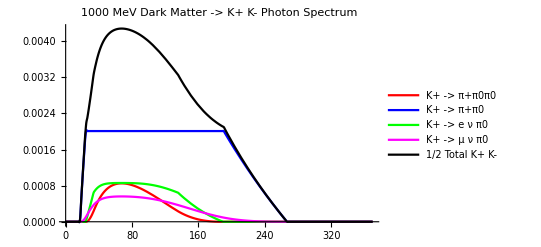

```mathematica
kplusminus[1000,370]
```

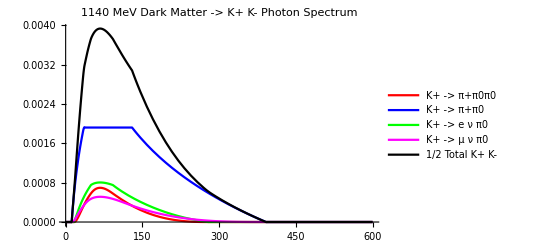

```mathematica
kplusminus[1140,600]
```

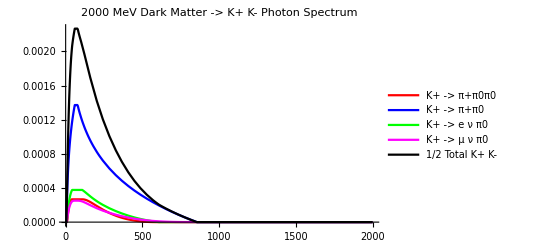

```mathematica
kplusminus[2000,2000]
```

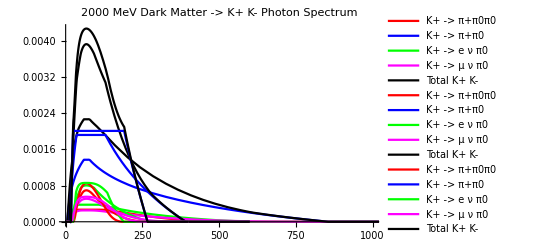

```mathematica
Show[{Out[752],Out[751],Out[750]}, PlotRange-> {{0,1000},Full}]
```

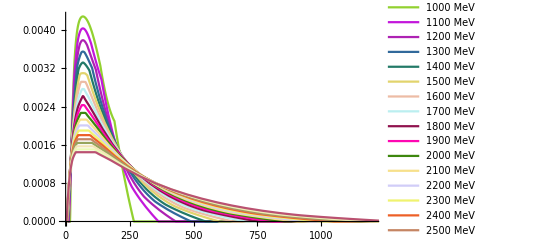

```mathematica
totalspreadpm[Table[1000+100*(i-1),{i,20}],1200]
```